```mathematica
Id = PauliMatrix[0];
X = PauliMatrix[1];
Y = PauliMatrix[2];
Z = PauliMatrix[3];
```

```mathematica
P[p_,i_,n_]:= KroneckerProduct @@ Table[If[m==i,p,Id],{m,1,n}]
PP[p_,i_,j_,n_]:= KroneckerProduct @@ Table[If[(m==i || m==j) && i≠j ,p,Id],{m,1,n}]
```

```mathematica
s:=12;
```

```mathematica
IntegerDigits[s,2,4]
```

{1,1,0,0}

```mathematica
Hm[n_] :=  Sum[If[IntegerDigits[s,2,n][[k]]==1,-P[(Z+Id)/2,k,n],0],{k,1,n}]
Hw[n_] :=  Sum[(PP[X,l,m,n] +PP[Y,l,m,n])/4 ,{l,1,n},{m,1,n}] -  (n/2)*(KroneckerProduct @@ Table[Id,{m,1,n}])
```

```mathematica
b = base[8,2]
```

{3,5,6,9,10,12,17,18,20,24,33,34,36,40,48,65,66,68,72,80,96,129,130,132,136,144,160,192}

```mathematica
adjMatEl[b[[1]],b[[23]],12]
```

1

```mathematica
adjMatElα[b[[1]],b[[23]],12,1.1]
```

0.143932

```mathematica
AdjMatα[8,2,0.1]
```

{{0,0.911586,0.884496,0.884496,0.873649,0,0.873649,0.870551,0,0,0.870551,0.873649,0,0,0,0.873649,0.884496,0,0,0,0,0.884496,0.911586,0,0,0,0,0},{0.911586,0,0.911586,0.911586,0,0.873649,0.884496,0,0.870551,0,0.873649,0,0.873649,0,0,0.870551,0,0.884496,0,0,0,0.873649,0,0.911586,0,0,0,0},{0.884496,0.911586,0,0,0.911586,0.884496,0,0.884496,0.873649,0,0,0.873649,0.870551,0,0,0,0.870551,0.873649,0,0,0,0,0.873649,0.884496,0,0,0,0},{0.884496,0.911586,0,0,0.911586,0.884496,0.911586,0,0,0.870551,0.884496,0,0,0.873649,0,0.873649,0,0,0.884496,0,0,0.870551,0,0,0.911586,0,0,0},{0.873649,0,0.911586,0.911586,0,0.911586,0,0.911586,0,0.873649,0,0.884496,0,0.870551,0,0,0.873649,0,0.873649,0,0,0,0.870551,0,0.884496,0,0,0},{0,0.873649,0.884496,0.884496,0.911586,0,0,0,0.911586,0.884496,0,0,0.884496,0.873649,0,0,0,0.873649,0.870551,0,0,0,0,0.870551,0.873649,0,0,0},{0.873649,0.884496,0,0.911586,0,0,0,0.911586,0.884496,0.873649,0.911586,0,0,0,0.873649,0.884496,0,0,0,0.884496,0,0.873649,0,0,0,0.911586,0,0},{0.870551,0,0.884496,0,0.911586,0,0.911586,0,0.911586,0.884496,0,0.911586,0,0,0.870551,0,0.884496,0,0,0.873649,0,0,0.873649,0,0,0.884496,0,0},{0,0.870551,0.873649,0,0,0.911586,0.884496,0.911586,0,0.911586,0,0,0.911586,0,0.873649,0,0,0.884496,0,0.870551,0,0,0,0.873649,0,0.873649,0,0},{0,0,0,0.870551,0.873649,0.884496,0.873649,0.884496,0.911586,0,0,0,0,0.911586,0.884496,0,0,0,0.884496,0.873649,0,0,0,0,0.873649,0.870551,0,0},{0.870551,0.873649,0,0.884496,0,0,0.911586,0,0,0,0,0.911586,0.884496,0.873649,0.870551,0.911586,0,0,0,0,0.884496,0.884496,0,0,0,0,0.911586,0},{0.873649,0,0.873649,0,0.884496,0,0,0.911586,0,0,0.911586,0,0.911586,0.884496,0.873649,0,0.911586,0,0,0,0.873649,0,0.884496,0,0,0,0.884496,0},{0,0.873649,0.870551,0,0,0.884496,0,0,0.911586,0,0.884496,0.911586,0,0.911586,0.884496,0,0,0.911586,0,0,0.870551,0,0,0.884496,0,0,0.873649,0},{0,0,0,0.873649,0.870551,0.873649,0,0,0,0.911586,0.873649,0.884496,0.911586,0,0.911586,0,0,0,0.911586,0,0.873649,0,0,0,0.884496,0,0.870551,0},{0,0,0,0,0,0,0.873649,0.870551,0.873649,0.884496,0.870551,0.873649,0.884496,0.911586,0,0,0,0,0,0.911586,0.884496,0,0,0,0,0.884496,0.873649,0},{0.873649,0.870551,0,0.873649,0,0,0.884496,0,0,0,0.911586,0,0,0,0,0,0.911586,0.884496,0.873649,0.870551,0.873649,0.911586,0,0,0,0,0,0.911586},{0.884496,0,0.870551,0,0.873649,0,0,0.884496,0,0,0,0.911586,0,0,0,0.911586,0,0.911586,0.884496,0.873649,0.870551,0,0.911586,0,0,0,0,0.884496},{0,0.884496,0.873649,0,0,0.873649,0,0,0.884496,0,0,0,0.911586,0,0,0.884496,0.911586,0,0.911586,0.884496,0.873649,0,0,0.911586,0,0,0,0.873649},{0,0,0,0.884496,0.873649,0.870551,0,0,0,0.884496,0,0,0,0.911586,0,0.873649,0.884496,0.911586,0,0.911586,0.884496,0,0,0,0.911586,0,0,0.870551},{0,0,0,0,0,0,0.884496,0.873649,0.870551,0.873649,0,0,0,0,0.911586,0.870551,0.873649,0.884496,0.911586,0,0.911586,0,0,0,0,0.911586,0,0.873649},{0,0,0,0,0,0,0,0,0,0,0.884496,0.873649,0.870551,0.873649,0.884496,0.873649,0.870551,0.873649,0.884496,0.911586,0,0,0,0,0,0,0.911586,0.884496},{0.884496,0.873649,0,0.870551,0,0,0.873649,0,0,0,0.884496,0,0,0,0,0.911586,0,0,0,0,0,0,0.911586,0.884496,0.873649,0.870551,0.873649,0.884496},{0.911586,0,0.873649,0,0.870551,0,0,0.873649,0,0,0,0.884496,0,0,0,0,0.911586,0,0,0,0,0.911586,0,0.911586,0.884496,0.873649,0.870551,0.873649},{0,0.911586,0.884496,0,0,0.870551,0,0,0.873649,0,0,0,0.884496,0,0,0,0,0.911586,0,0,0,0.884496,0.911586,0,0.911586,0.884496,0.873649,0.870551},{0,0,0,0.911586,0.884496,0.873649,0,0,0,0.873649,0,0,0,0.884496,0,0,0,0,0.911586,0,0,0.873649,0.884496,0.911586,0,0.911586,0.884496,0.873649},{0,0,0,0,0,0,0.911586,0.884496,0.873649,0.870551,0,0,0,0,0.884496,0,0,0,0,0.911586,0,0.870551,0.873649,0.884496,0.911586,0,0.911586,0.884496},{0,0,0,0,0,0,0,0,0,0,0.911586,0.884496,0.873649,0.870551,0.873649,0,0,0,0,0,0.911586,0.873649,0.870551,0.873649,0.884496,0.911586,0,0.911586},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.911586,0.884496,0.873649,0.870551,0.873649,0.884496,0.884496,0.873649,0.870551,0.873649,0.884496,0.911586,0}}

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"]
```

```mathematica
<<MaTeX`
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
SetOptions[MaTeX,"FontSize"-> 24, "Magnification"->1]
texStyle={FontFamily->"Latin Modern Roman",FontSize->20}
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→24,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

{FontFamily→Latin Modern Roman,FontSize→20}

```mathematica
Subspace specific spatial search
```

```mathematica
base[n_,s_]:= Table[If[Total[IntegerDigits[k,2,n]]==s,k,Unevaluated@Sequence[]], {k,0,2^n-1}]
markMatEl[l_,m_,n_,mark_]:=If[l==m,-HammingDistance[IntegerDigits[l,2,n],IntegerDigits[mark,2,n]]/2,0]
adjMatEl[l_,m_,n_]:=If[HammingDistance[IntegerDigits[l,2,n],IntegerDigits[m,2,n]]==2,1,0]
(*adjMatElα[l_,m_,n_,α_]:=If[HammingDistance[IntegerDigits[l,2,n],IntegerDigits[m,2,n]]==2,1/(Abs[Subtract @@ Flatten[Position[Abs[IntegerDigits[l,2,n] - IntegerDigits[m,2,n]],1]]])^α,0]*)
adjMatElα[l_,m_,n_,α_]:=If[HammingDistance[IntegerDigits[l,2,n],IntegerDigits[m,2,n]]==2,1/2(1/(Abs[Subtract @@ Flatten[Position[Abs[IntegerDigits[l,2,n] - IntegerDigits[m,2,n]],1]]])^α + 1/(n - Abs[Subtract @@ Flatten[Position[Abs[IntegerDigits[l,2,n] - IntegerDigits[m,2,n]],1]]])^α),0]
adjMatCompEl[l_,m_,n_]:=If[l==m||HammingDistance[IntegerDigits[l,2,n],IntegerDigits[m,2,n]]==2,0,1]
adjMatMarkEl[l_,m_,n_, mark_,p1_,p2_]:=If[adjMatEl[l,m,n] ==1 && p1[l,mark] && p2[m,mark] ,1,0]
adjMatCompMarkEl[l_,m_,n_, mark_,p1_,p2_]:=If[adjMatCompEl[l,m,n] ==1 && p1[l,mark] && p2[m,mark] ,1,0]
AdjMat[n0_,s0_]:=Module[{n=n0,s=s0},
b = base[n,s];
Table[Table[adjMatEl[b[[i]],b[[j]],n],{j,1,Length[b]}],{i,1, Length[b]}]
]
AdjMatα[n0_,s0_,α0_]:=Module[{n=n0,s=s0, α=α0},
b = base[n,s];
Table[Table[adjMatElα[b[[i]],b[[j]],n,α],{j,1,Length[b]}],{i,1, Length[b]}]
]
AdjMatComp[n0_,s0_]:=Module[{n=n0,s=s0},
b = base[n,s];
Table[Table[adjMatCompEl[b[[i]],b[[j]],n],{j,1,Length[b]}],{i,1, Length[b]}]
]
AdjMatMark[n0_,s0_,mark0_, pos10_,pos20_]:=Module[{n=n0,s=s0, mark=mark0,pos1=pos10,pos2=pos20},
b = base[n,s];
p1 = Which[pos1==0,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==0],pos1==1,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==2],pos1==2, Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]>2]];
p2 = Which[pos2==0,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==0],pos2==1,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==2],pos2==2, Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]>2]];
Table[Table[adjMatMarkEl[b[[i]],b[[j]],mark,n,p1,p2],{j,1,Length[b]}],{i,1, Length[b]}]
]
AdjMatCompMark[n0_,s0_,mark0_, pos10_,pos20_]:=Module[{n=n0,s=s0, mark=mark0,pos1=pos10,pos2=pos20},
b = base[n,s];
p1 = Which[pos1==0,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==0],pos1==1,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==2],pos1==2, Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]>2]];
p2 = Which[pos2==0,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==0],pos2==1,Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]==2],pos2==2, Function[{a,b},HammingDistance[IntegerDigits[a,2,n],IntegerDigits[b,2,n]]>2]];
Table[Table[adjMatCompMarkEl[b[[i]],b[[j]],mark,n,p1,p2],{j,1,Length[b]}],{i,1, Length[b]}]
]
MarkMat[n0_,s0_,mark0_]:=Module[{n=n0,s=s0, mark=mark0},
b = base[n,s];
dim = Length[b];
s/2  IdentityMatrix[dim]+Table[Table[markMatEl[b[[i]],b[[j]],n,mark],{j,1,dim}],{i,1, dim}]
]
Fidelities[nbits0_,subspace0_, γ0_,tmax0_]:=Module[{nbits=nbits0,s=subspace0,γ=γ0,tmax=tmax0},
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMat[nbits,s];
Hmark =MarkMat[nbits,s,mark];
int=100;
Δt =N[tmax/int];
unitary:=MatrixExp[-I Δt(γ Hwalk+Hmark)];
update[state_]:= unitary.state;
initVec = Table[ 1/√dim,{k,1,dim}];
markVec = Table[If[b[[i]]==mark,1,0],{i,1,dim}];
states = NestList[update,initVec,int];
fidelities = Abs[markVec.#]^2&/@ states;
Transpose[{Table[i*Δt,{i,0,int}],fidelities}]
] 
Fidelitiesα[nbits0_,subspace0_, γ0_,tmax0_,α0_]:=Module[{nbits=nbits0,s=subspace0,γ=γ0,tmax=tmax0, α=α0},
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMatα[nbits,s,α];
Hmark =MarkMat[nbits,s,mark];
int=100;
Δt =N[tmax/int];
unitary:=N[MatrixExp[-I Δt(γ Hwalk+Hmark)]];
update[state_]:= unitary.state;
initVec = Table[ 1/√dim,{k,1,dim}];
markVec = Table[If[b[[i]]==mark,1,0],{i,1,dim}];
states = NestList[update,initVec,int];
fidelities = Abs[markVec.#]^2&/@ states;
Transpose[{Table[i*Δt,{i,0,int}],fidelities}]
] 
FidelitiesSuperposition[nbits0_,subspace0_, γ0_,tmax0_]:=Module[{nbits=nbits0,s=subspace0,γ=γ0,tmax=tmax0},
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMat[nbits,s];
Hmark =MarkMat[nbits,s,mark];
int=100;
Δt =N[tmax/int];
unitary:=MatrixExp[-I Δt(γ Hwalk+Hmark)];
update[state_]:= unitary.state;
initVec = Table[ 1/√dim,{k,1,dim}];
markVec = Table[If[b[[i]]==mark,1,0],{i,1,dim}];
initminusmarkVec = Table[ If[b[[k]]≠mark,1/√dim,0],{k,1,dim}];
states = NestList[update,initVec,int];
times = Table[i*Δt,{i,0,int}];
{Transpose[{times,Abs[markVec.#]^2&/@ states}],Transpose[{times,Abs[initVec.#]^2&/@ states}],
Transpose[{times,Abs[initminusmarkVec.#]^2&/@ states}],
Transpose[{times,Abs[initminusmarkVec.#]^2+ Abs[markVec.#]^2&/@ states}]}
] 
FidelitiesSubspaces[nbits0_,subspace0_, γ0_,tmax0_]:=Module[{nbits=nbits0,s=subspace0,γ=γ0,tmax=tmax0},
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMat[nbits,s];
Hmark =MarkMat[nbits,s,mark];
int=100;
Δt =N[tmax/int];
unitary:=MatrixExp[-I Δt(γ Hwalk+Hmark)];
update[state_]:= unitary.state;
initVec = Table[ 1/√dim,{k,1,dim}];
mark0Vec = Table[If[Hmark[[i,i]]==s,1,0],{i,1,dim}];
mark1Vec = Normalize[Table[If[Hmark[[i,i]]==0,1,0],{i,1,dim}]];
mark2Vec = Normalize[Table[If[Hmark[[i,i]]==-s,1,0],{i,1,dim}]];
states = NestList[update,initVec,int];
times = Table[i*Δt,{i,0,int}];
{Transpose[{times,Abs[mark0Vec.#]^2&/@ states}],Transpose[{times,Abs[mark1Vec.#]^2&/@ states}],
Transpose[{times,Abs[mark2Vec.#]^2&/@ states}],
Transpose[{times,Abs[initVec.#]^2&/@ states}]}
]
Fidelitiesk[nbits0_,subspace0_, γ0_,tmax0_,k0_]:=Module[{nbits=nbits0,s=subspace0,γ=γ0,tmax=tmax0, k=k0},
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMat[nbits,s];
Hmark =MarkMat[nbits,s,mark];
int=100;
Δt =N[tmax/int];
unitary:=MatrixExp[-I Δt(γ Hwalk+Hmark)];
update[state_]:= unitary.state;
initVec = Table[ 1/√dim,{k,1,dim}];
kVec = Table[If[b[[i]]==mark,1,0],{i,1,dim}];
states = NestList[update,initVec,int];
fidelities = Abs[kVec.#]^2&/@ states;
Transpose[{Table[i*Δt,{i,0,int}],fidelities}]
] 
Spectra[nbits0_,subspace0_, γ0_]:=
Module[{nbits=nbits0,s=subspace0,γ=γ0},
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMat[nbits,s];
Hmark =MarkMat[nbits,s,mark];
{Eigenvalues[γ Hwalk],Eigenvalues[Hmark],Eigenvalues[γ Hwalk + Hmark]}
]
```

```mathematica
Clear[k]
```

```mathematica
numberK[n_,k_]:=Binomial[n,k];
dis[n_,k_,q_]:=If[q==0,1,Binomial[k,q]Binomial[n-k,q]];
Hsearch[n_,k_] := Table[Table[If[i==j,(i-1)(n-2(i-1)),If[Abs[j-i]==1,Min[i,j]Sqrt[(k-Min[i,j]+1)(n-k-Min[i,j]+1)],0]],{i,1,k+1}],{j,1,k+1}];
Hmarked[k_]:=DiagonalMatrix[Table[k/2-(i-1),{i,1,k+1}]];
HsearchTotal[n_,k_,γ_]:= γ Hsearch[n,k]+Hmarked[k];
superpositionVec[n_,k_]:=Table[Sqrt[dis[n,k,i-1]],{i,1,k+1}]/Sqrt[numberK[n,k]];
markedVec[k_]:=UnitVector[k+1,1];
FidelityAnalytical[nbits_,subspace_,γ_,t_]:= Abs[ markedVec[subspace].MatrixExp[I HsearchTotal[nbits,subspace,γ] t].superpositionVec[nbits,subspace]]^2
AsymptoticH[k_] := Table[Table[If[Abs[j-i]==1,Min[i,j]Sqrt[(k+1-Min[i,j])],0],{i,1,k+1}],{j,1,k+1}];
FidelityAsymptotic[subspace_,t_]:= Abs[ UnitVector[subspace+1,1].MatrixExp[I AsymptoticH[subspace] t]. UnitVector[subspace+1,subspace+1]]^2
```

0.835505

5.1

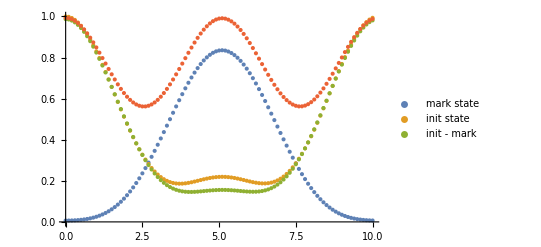

```mathematica
nodes = 18;
fids = FidelitiesSuperposition[nodes,2,N[1/(nodes-2)],10];
markfids = fids[[1]];
maxfidelity=Max[markfids[[All,2]]]
time = markfids[[All,1]][[Ordering[markfids[[All,2]],-1][[1]]]]
ListPlot[fids,PlotLegends->{"mark state","init state", "init - mark"}]
```

```mathematica
Clear[Hs]
```

```mathematica
AsymptoticH[4] // MatrixForm
```

(0 | 2 | 0 | 0 | 0
2 | 0 | 2 √3 | 0 | 0
0 | 2 √3 | 0 | 3 √2 | 0
0 | 0 | 3 √2 | 0 | 4
0 | 0 | 0 | 4 | 0)

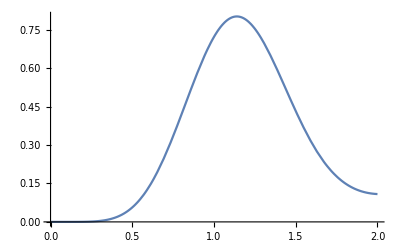

```mathematica
Plot[FidelityAsymptotic[3,t],{t,0,2}]
```

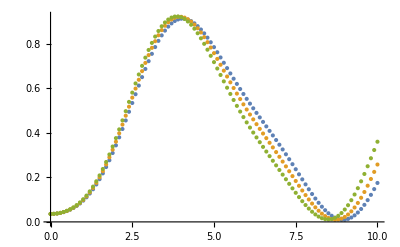

```mathematica
ListPlot[{Fidelities[8,2, 0.115,10],Fidelities[8,2, 0.12,10],Fidelities[8,2, 0.125,10]}]
```

```mathematica
ListPlot[{Fidelitiesα[8,2, 0.115,10,0],Fidelitiesα[8,2, 0.12,10,0],Fidelitiesα[8,2, 0.125,10,0]}]
```

-Graphics-

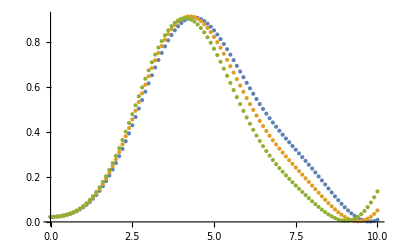

```mathematica
ListPlot[{Fidelitiesα[10,2, 0.095,10,0],Fidelitiesα[10,2, 0.10,10,0],Fidelitiesα[10,2, 0.105,10,0]}]
```

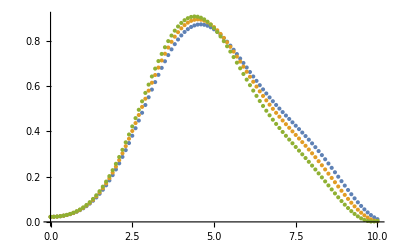

```mathematica
ListPlot[{Fidelitiesα[10,2, 0.115,10,0.2],Fidelitiesα[10,2, 0.12,10,0.2],Fidelitiesα[10,2, 0.125,10,0.2]}]
```

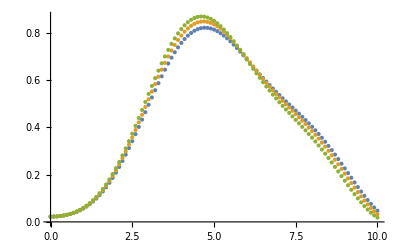

```mathematica
ListPlot[{Fidelitiesα[10,2, 0.14,10,0.4],Fidelitiesα[10,2, 0.145,10,0.4],Fidelitiesα[10,2, 0.15,10,0.4]}]
```

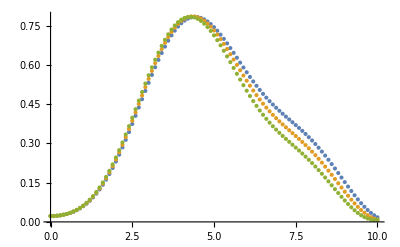

```mathematica
ListPlot[{Fidelitiesα[10,2, 0.165,10,0.6],Fidelitiesα[10,2, 0.17,10,0.6],Fidelitiesα[10,2, 0.175,10,0.6]}]
```

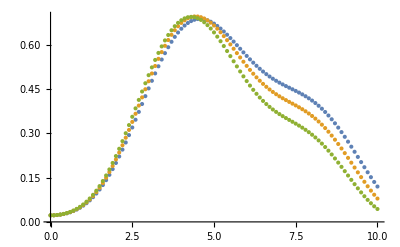

```mathematica
ListPlot[{Fidelitiesα[10,2, 0.18,10,0.8],Fidelitiesα[10,2, 0.19,10,0.8],Fidelitiesα[10,2, 0.20,10,0.8]}]
```

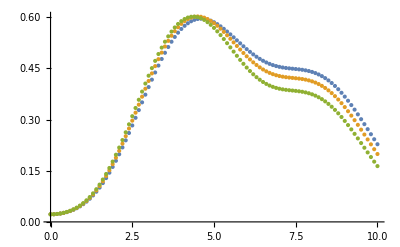

```mathematica
ListPlot[{Fidelitiesα[10,2, 0.20,10,1],Fidelitiesα[10,2, 0.21,10,1],Fidelitiesα[10,2, 0.22,10,1]}]
```

```mathematica
FindMaxγ[10,2,1]
```

FindMaxγ[10,2,1]

```mathematica
FindMaxγ[10,2,1.5]
```

{0.216364,0.618647}

```mathematica
FindMaxγ[10,2,2]
```

{0.25051,0.569977}

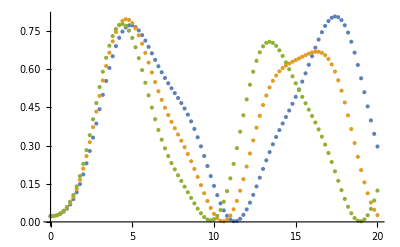

```mathematica
ListPlot[{Fidelitiesα[10,2,0.14,20,1],Fidelitiesα[10,2, 0.15590190371923973,20,1],Fidelitiesα[10,2, 0.17,20,1]}]
```

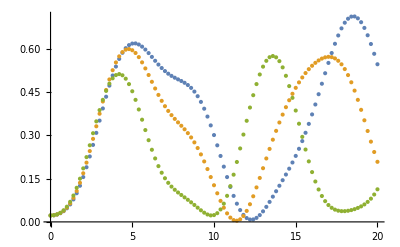

```mathematica
ListPlot[{Fidelitiesα[10,2,0.21636420728739353,20,1.5],Fidelitiesα[10,2, 0.24,20,1.5],Fidelitiesα[10,2, 0.28,20,1.5]}]
```

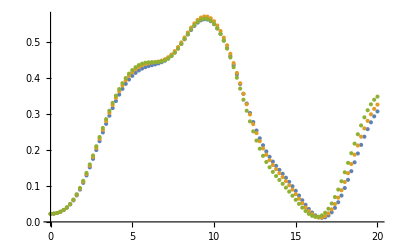

```mathematica
ListPlot[{Fidelitiesα[10,2,0.24,20,2],Fidelitiesα[10,2, 0.25051049231803624,20,2],Fidelitiesα[10,2, 0.26,20,2]}]
```

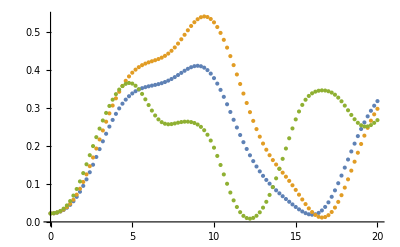

```mathematica
ListPlot[{Fidelitiesα[10,2,0.2,20,2],Fidelitiesα[10,2, 0.23,20,2],Fidelitiesα[10,2, 0.34,20,2]}]
```

```mathematica
AdjMatα[n0_,s0_,α0_]:=Module[{n=n0,s=s0, α=α0},
b = base[n,s];
Table[Table[adjMatElα[b[[i]],b[[j]],n,α],{j,1,Length[b]}],{i,1, Length[b]}]
]
```

```mathematica
b
```

{1,2,4,8,16,32,64,128}

```mathematica
b[[3]]
```

4

```mathematica
adjMatElα[b[[3]],b[[1]],nbits,α]
```

2/3

```mathematica
adjMatElα[b[[2]],b[[8]],nbits,α]
```

2/3

```mathematica
IntegerDigits[b[[1]],2,nbits]
```

{0,0,0,0,0,0,0,1}

```mathematica
IntegerDigits[b[[2]],2,nbits]
```

{0,0,0,0,0,0,1,0}

```mathematica
Abs[Subtract @@Flatten[Position[Abs[IntegerDigits[b[[1]],2,nbits] - IntegerDigits[b[[8]],2,nbits]],1]]]
```

7

```mathematica
1/(Abs[Subtract @@Flatten[Position[Abs[IntegerDigits[b[[1]],2,nbits] - IntegerDigits[b[[2]],2,nbits]],1]]])^α + 1/(nbits - (Abs[Subtract @@ Flatten[Position[Abs[IntegerDigits[b[[1]],2,nbits] - IntegerDigits[b[[2]],2,nbits]],1]]]))^α
```

8/7

```mathematica
Subtract @@ Flatten[Position[Abs[IntegerDigits[b[[1]],2,nbits] - IntegerDigits[b[[8]],2,nbits]],1]]
```

-7

```mathematica
{7,8}
```

```mathematica
nbits=8;
s=1;
α=1;
b = base[nbits, s];
dim = Length[b];
mark := b[[6]];
Hwalk= AdjMatα[nbits,s,α];
Hmark =MarkMat[nbits,s,mark];
int=100;
Δt =N[tmax/int];
unitary:=N[MatrixExp[-I Δt(γ Hwalk+Hmark)]];
Hwalk // MatrixForm  // N
```

(0. | 1.14286 | 0.666667 | 0.533333 | 0.5 | 0.533333 | 0.666667 | 1.14286
1.14286 | 0. | 1.14286 | 0.666667 | 0.533333 | 0.5 | 0.533333 | 0.666667
0.666667 | 1.14286 | 0. | 1.14286 | 0.666667 | 0.533333 | 0.5 | 0.533333
0.533333 | 0.666667 | 1.14286 | 0. | 1.14286 | 0.666667 | 0.533333 | 0.5
0.5 | 0.533333 | 0.666667 | 1.14286 | 0. | 1.14286 | 0.666667 | 0.533333
0.533333 | 0.5 | 0.533333 | 0.666667 | 1.14286 | 0. | 1.14286 | 0.666667
0.666667 | 0.533333 | 0.5 | 0.533333 | 0.666667 | 1.14286 | 0. | 1.14286
1.14286 | 0.666667 | 0.533333 | 0.5 | 0.533333 | 0.666667 | 1.14286 | 0.)

```mathematica
m=
If[HammingDistance[IntegerDigits[l,2,nbits],IntegerDigits[m,2,nbits]]==2,1/(Abs[Subtract @@ Flatten[Position[Abs[IntegerDigits[l,2,nbits] - IntegerDigits[m,2,nbits]],1]]])^α + 1/(Abs[n - (Subtract @@ Flatten[Position[Abs[IntegerDigits[l,2,nbits] - IntegerDigits[m,2,nbits]],1]])])^α,0]
```

(0. | 1.11111 | 0.6 | 0.424242 | 0.333333 | 0.276923 | 0.238095 | 0.209524
1.11111 | 0. | 1.11111 | 0.6 | 0.424242 | 0.333333 | 0.276923 | 0.238095
0.6 | 1.11111 | 0. | 1.11111 | 0.6 | 0.424242 | 0.333333 | 0.276923
0.424242 | 0.6 | 1.11111 | 0. | 1.11111 | 0.6 | 0.424242 | 0.333333
0.333333 | 0.424242 | 0.6 | 1.11111 | 0. | 1.11111 | 0.6 | 0.424242
0.276923 | 0.333333 | 0.424242 | 0.6 | 1.11111 | 0. | 1.11111 | 0.6
0.238095 | 0.276923 | 0.333333 | 0.424242 | 0.6 | 1.11111 | 0. | 1.11111
0.209524 | 0.238095 | 0.276923 | 0.333333 | 0.424242 | 0.6 | 1.11111 | 0.)

```mathematica
prob[k_,s_] :=N[Sum[(-1)^(i+1)Binomial[k,i]((k-i)/k)^s,{i,1,k}] ]
```

```mathematica
prob[1,1]
```

0

```mathematica
prob[2,8]
```

0.0078125

```mathematica
prob[3,15]
```

0.00685077

```mathematica
prob[4,21]
```

0.00951077

```mathematica
prob[5,28]
```

0.00966527

```mathematica
GoldenSearch[fun0_,a0_,b0_,tol0_,maxiter0_]:=Module[{fun=fun0,a=a0,b=b0, tol=tol0,maxiter=maxiter0},
{ψ,ϕ}={1-1/GoldenRatio,1/GoldenRatio}//N;
m1=Rescale[ψ,{0,1},{a,b}];
m2=Rescale[ϕ,{0,1},{a,b}];
f1=fun[m1];
f2=fun[m2];
k=0;
While[Abs[b-a]>tol (Abs[m1]+Abs[m2])&&k<maxiter,k=k+1;
If[f1>f2,b=m2;m2=m1;m1=ψ a+ϕ m2;
f2=f1;f1=fun[m1],a=m1;m1=m2;m2=ϕ m1+ψ b;
f1=f2;f2=fun[m2]];
(*Print[{k,a,m1,m2,b}]*)];
If[k==maxiter, Print["Max interations reached"]];
γ=(a+b)/2;
{γ,fun[γ]}
]
```

```mathematica
FindMaxγ0[nbits0_,k0_]:= Module[{nbits=nbits0,k=k0}, 
max[γ_]:=Max[Transpose[Fidelities[nbits,k, γ,10]][[2]]];
maxγ = GoldenSearch[max, 0.7/nbits,1.8 k/nbits,0.001,15];
(*Print[maxγ];*)
maxγ
]
```

```mathematica
FindMaxγ[nbits0_,k0_,α0_]:= Module[{nbits=nbits0,k=k0, α=α0}, 
max[γ_]:=Max[Transpose[Fidelitiesα[nbits,k, γ,20,α]][[2]]];
maxγ = GoldenSearch[max, 0.7 (1+α)/nbits,1.8 k(1+α)/nbits,0.001,100];
(*Print[maxγ];*)
maxγ
]
```

```mathematica
FindMaxγα[nbits0_,k0_,α0_]:= Module[{nbits=nbits0,k=k0, α=α0}, 
max[γ_]:=Max[Transpose[Fidelitiesα[nbits,k, γ,20,α]][[2]]];
maxγ = GoldenSearch[max,0.7 (1+α)/nbits,1.8 k(1+α)/nbits,0.001,100];
(*Print[maxγ];*)
{α,maxγ[[2]]}
]
```

```mathematica
With[{nbits=12,k=1,α=0},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,1,0]
```

{0.0583333,1/6}

{0.0835363,0.999891}

```mathematica
With[{nbits=12,k=1,α=1.5},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,1,1.5]
```

{0.145833,0.416667}

{0.374644,0.783381}

```mathematica
With[{nbits=12,k=3,α=0},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,3,0]
```

{0.0583333,1/2}

{0.0823606,0.857447}

```mathematica
With[{nbits=12,k=3,α=1.5},{0.7(1+α)/nbits,2 (1+α)/nbits}]
```

{0.145833,0.416667}

```mathematica
With[{nbits=12,k=3,α=1.5},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,3,1.5]
```

{0.145833,1.25}

{0.405428,0.573694}

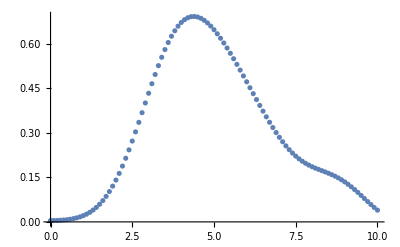

```mathematica
ListPlot[{Fidelitiesα[12,3,0.29,10,1]}]
```

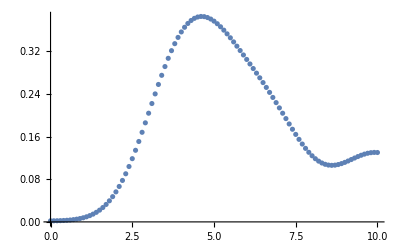

```mathematica
ListPlot[{Fidelitiesα[12,4,0.42,10,1.5]}]
```

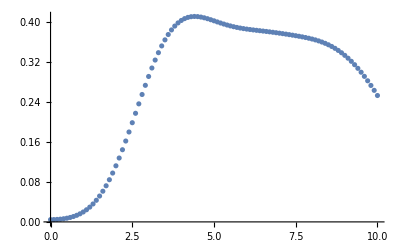

```mathematica
ListPlot[{Fidelitiesα[12,3,0.4,10,1.5]}]
```

```mathematica
With[{nbits=12,k=3,α=1.5},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,3,1.5]
```

{0.145833,1.25}

{0.429312,0.418749}

```mathematica
With[{nbits=12,k=4,α=0},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,4,0]
```

{0.0583333,2/3}

{0.0822635,0.823979}

```mathematica
With[{nbits=12,k=4,α=1.5},{0.7(1+α)/nbits,2 (1+α)/nbits}]
```

{0.145833,0.416667}

```mathematica
With[{nbits=12,k=4,α=1.5},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,4,1.5]
```

{0.145833,1.66667}

{0.414356,0.385139}

```mathematica
Transpose[Fidelitiesα[10,2, 0.2,10,1]][[2]]
```

{1/45,0.022465,0.0232008,0.0244518,0.0262538,0.0286552,0.031715,0.0355003,0.0400843,0.0455429,0.0519518,0.0593837,0.0679048,0.0775725,0.0884321,0.100515,0.113835,0.128391,0.14416,0.161102,0.179154,0.198236,0.21825,0.239079,0.260591,0.28264,0.305069,0.327711,0.350395,0.372943,0.395177,0.416923,0.438007,0.458266,0.477544,0.495696,0.512591,0.528112,0.54216,0.554652,0.565525,0.574734,0.582256,0.588086,0.59224,0.594753,0.595681,0.595096,0.593088,0.589764,0.585244,0.57966,0.573155,0.56588,0.55799,0.549643,0.540998,0.53221,0.523429,0.514795,0.506437,0.498473,0.491,0.484101,0.477839,0.472254,0.467368,0.463178,0.459662,0.456777,0.454461,0.452633,0.451198,0.450048,0.449064,0.448122,0.447093,0.445846,0.444255,0.4422,0.439568,0.436258,0.432182,0.427271,0.421468,0.414737,0.407062,0.398441,0.388896,0.37846,0.367188,0.355146,0.342413,0.329079,0.315243,0.301008,0.286484,0.271778,0.256999,0.242253,0.227641}

```mathematica
FindMaxγα[8,2,0.1]
```

{0.1,0.921532}

```mathematica
Fα81 =Table[FindMaxγα[8,1,α] ,{α,0,1.5,0.05}];
Fα91 =Table[FindMaxγα[9,1,α] ,{α,0,1.5,0.05}];
Fα101 =Table[FindMaxγα[10,1,α] ,{α,0,1.5,0.05}];
Fα111 =Table[FindMaxγα[11,1,α] ,{α,0,1.5,0.05}];
Fα121 =Table[FindMaxγα[12,1,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_1.dat",Fα81]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_1.dat",Fα91]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_1.dat",Fα101]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_1.dat",Fα111]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_1.dat",Fα121]
```

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_1.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_1.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_1.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_1.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_1.dat

```mathematica
Fα82 =Table[FindMaxγα[8,2,α] ,{α,0,1.5,0.05}];
Fα92 =Table[FindMaxγα[9,2,α] ,{α,0,1.5,0.05}];
Fα102 =Table[FindMaxγα[10,2,α] ,{α,0,1.5,0.05}];
Fα112 =Table[FindMaxγα[11,2,α] ,{α,0,1.5,0.05}];
Fα122 =Table[FindMaxγα[12,2,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_2.dat",Fα82]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_2.dat",Fα92]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_2.dat",Fα102]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_2.dat",Fα112]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_2.dat",Fα122]
```

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_2.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_2.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_2.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_2.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_2.dat

```mathematica
Fα83=Table[FindMaxγα[8,3,α] ,{α,0,1.5,0.05}];
Fα93=Table[FindMaxγα[9,3,α] ,{α,0,1.5,0.05}] ;
Fα103=Table[FindMaxγα[10,3,α] ,{α,0,1.5,0.05}];
Fα113=Table[FindMaxγα[11,3,α] ,{α,0,1.5,0.05}];
Fα123=Table[FindMaxγα[12,3,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_3.dat",Fα83]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_3.dat",Fα93]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_3.dat",Fα103]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_3.dat",Fα113]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_3.dat",Fα123]
```

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_3.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_3.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_3.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_3.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_3.dat

```mathematica
Fα84 =Table[FindMaxγα[8,4,α] ,{α,0,1.5,0.05}];
Fα94 =Table[FindMaxγα[9,4,α] ,{α,0,1.5,0.05}];
Fα104 =Table[FindMaxγα[10,4,α] ,{α,0,1.5,0.05}];
Fα114 =Table[FindMaxγα[11,4,α] ,{α,0,1.5,0.05}];
Fα124 =Table[FindMaxγα[12,4,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_4.dat",Fα84]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_4.dat",Fα94]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_4.dat",Fα104]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_4.dat",Fα114]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_4.dat",Fα124]
```

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_4.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_4.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_4.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_4.dat

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_4.dat

```mathematica
Fα85 =Table[FindMaxγα[8,5,α] ,{α,0,1.5,0.05}];
Fα95 =Table[FindMaxγα[9,5,α] ,{α,0,1.5,0.05}];
Fα105 =Table[FindMaxγα[10,5,α] ,{α,0,1.5,0.05}];
Fα115 =Table[FindMaxγα[11,5,α] ,{α,0,1.5,0.05}];
Fα125 =Table[FindMaxγα[12,5,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_5.dat",Fα85]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_5.dat",Fα95]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_5.dat",Fα105]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_5.dat",Fα115]
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_5.dat",Fα125]
```

```mathematica
Fα123 =Table[FindMaxγα[12,3,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_3.dat",Fα125]
```

```mathematica
Fα124 =Table[FindMaxγα[12,4,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_4.dat",Fα125]
```

```mathematica
Fα125 =Table[FindMaxγα[12,5,α] ,{α,0,1.5,0.05}];
Export["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_5.dat",Fα125]
```

/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_5.dat

```mathematica
Fα81 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_1.dat"];
Fα82 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_2.dat"];
Fα83 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_3.dat"];
Fα84 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_4.dat"];
Fα85 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_k_5.dat"];
```

```mathematica
Fα91 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_1.dat"];
Fα92 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_2.dat"];
Fα93 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_3.dat"];
Fα94 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_4.dat"];
Fα95 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_9_k_5.dat"];
```

```mathematica
Fα101 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_1.dat"];
Fα102 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_2.dat"];
Fα103 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_3.dat"];
Fα104 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_4.dat"];
Fα105 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_10_k_5.dat"];
```

```mathematica
Fα111 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_1.dat"];
Fα112 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_2.dat"];
Fα113 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_3.dat"];
Fα114 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_4.dat"];
Fα115 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_11_k_5.dat"];
```

```mathematica
Fα121 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_1.dat"];
Fα122 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_2.dat"];
Fα123 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_3.dat"];
Fα124 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_4.dat"];
Fα125 = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_12_k_5.dat"];
```

```mathematica
{Fα81,Fα91,Fα101,Fα111,Fα121} = Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_9_10_11_12_k_1.dat"]
```

```mathematica
Import["/Users/dylan/Documents/Physics/Mathematica/spatial_search/Falpha_n_8_9_10_11_12_k_1.dat", "Table"]
```

{{{0.,,0.9998463060472237},{0.05,,0.9998266259302229},{0.1,,0.9997574486394144},{0.15000000000000002,,0.9996230472676887},{0.2,,0.9994036254277322},{0.25,,0.9990785001045626},{0.30000000000000004,,0.998623361662926},{0.35000000000000003,,0.9980134367313277},{0.4,,0.9972198900129746},{0.45,,0.9962128809183383},{0.5,,0.9949622642982037},{0.55,,0.9934342711311068},{0.6000000000000001,,0.9916450793294256},{0.65,,0.9895052910216529},{0.7000000000000001,,0.9869962345760771},{0.75,,0.9840878316122097},{0.8,,0.9807509001452515},{0.8500000000000001,,0.9769613388805157},{0.9,,0.9726961585672113},{0.9500000000000001,,0.9679386489731332},{1.,,0.9626759110620681},{1.05,,0.9569022294857052},{1.1,,0.9506163217386957},{1.1500000000000001,,0.94382371364524},{1.2000000000000002,,0.9365375696164102},{1.25,,0.9287753700984571},{1.3,,0.9205624954574743},{1.35,,0.9119449928846538},{1.4000000000000001,,0.9031093180746088},{1.4500000000000002,,0.8939417182253763},{1.5,,0.8844870476453349}},{{0.,,0.999988103174901},{0.05,,0.9999681099621551},{0.1,,0.9998977336566982},{0.15000000000000002,,0.9997586834071049},{0.2,,0.9995308837019626},{0.25,,0.9991897048874051},{0.30000000000000004,,0.9987097186130182},{0.35000000000000003,,0.9980597997162672},{0.4,,0.9972070872541459},{0.45,,0.9961164452005692},{0.5,,0.9947515413535553},{0.55,,0.9930701672433951},{0.6000000000000001,,0.9910340368257381},{0.65,,0.9886011706980213},{0.7000000000000001,,0.9857303156726297},{0.75,,0.9823830880546756},{0.8,,0.9785229852482985},{0.8500000000000001,,0.9741526449181829},{0.9,,0.9692760566698065},{0.9500000000000001,,0.9638129718320343},{1.,,0.9577486275147039},{1.05,,0.9510754130811583},{1.1,,0.9437946828926992},{1.1500000000000001,,0.9359162926617395},{1.2000000000000002,,0.9274587475691423},{1.25,,0.9184497506412118},{1.3,,0.9090665263813695},{1.35,,0.8993052905661889},{1.4000000000000001,,0.8891371175664109},{1.4500000000000002,,0.8786198201168789},{1.5,,0.8679808426456582}},{{0.,,0.9999226700641556},{0.05,,0.9999034619380304},{0.1,,0.99983493188348},{0.15000000000000002,,0.9996990048583254},{0.2,,0.9994737711848756},{0.25,,0.9991338947816895},{0.30000000000000004,,0.9986506196482635},{0.35000000000000003,,0.9979907306884175},{0.4,,0.99711920288361},{0.45,,0.9959937314533723},{0.5,,0.9945733075994441},{0.55,,0.992810173310419},{0.6000000000000001,,0.990657320109548},{0.65,,0.9880653623725097},{0.7000000000000001,,0.9849857405970864},{0.75,,0.9813706805862129},{0.8,,0.9771759886103918},{0.8500000000000001,,0.9723609971073239},{0.9,,0.9668914701757373},{0.9500000000000001,,0.9607413275504179},{1.,,0.9539901745469753},{1.05,,0.94661301368943},{1.1,,0.9385447084586723},{1.1500000000000001,,0.9297981415936197},{1.2000000000000002,,0.9204004401784411},{1.25,,0.9104186629942627},{1.3,,0.9001220620765866},{1.35,,0.8893304111260513},{1.4000000000000001,,0.87810998166514},{1.4500000000000002,,0.8668470844050422},{1.5,,0.8553705219917839}},{{0.,,0.9999935841313563},{0.05,,0.9999748921890402},{0.1,,0.9999079655320259},{0.15000000000000002,,0.9997739833834027},{0.2,,0.9995499686045258},{0.25,,0.9992110078200358},{0.30000000000000004,,0.9987243843766771},{0.35000000000000003,,0.9980548170793282},{0.4,,0.9971630688537674},{0.45,,0.996003308275248},{0.5,,0.9945283113800613},{0.55,,0.9926847356467011},{0.6000000000000001,,0.9904166762214069},{0.65,,0.9876686927442366},{0.7000000000000001,,0.9843815124883626},{0.75,,0.9806176481657359},{0.8,,0.9762189670794644},{0.8500000000000001,,0.971138702892742},{0.9,,0.9653359721077499},{0.9500000000000001,,0.9587781095865844},{1.,,0.9514439605926718},{1.05,,0.943323840693775},{1.1,,0.9346367955902802},{1.1500000000000001,,0.9252303148235275},{1.2000000000000002,,0.9151083517141224},{1.25,,0.9043453919093121},{1.3,,0.8932757408155895},{1.35,,0.8816766416660803},{1.4000000000000001,,0.8693352600814221},{1.4500000000000002,,0.8553844929115304},{1.5,,0.8403549719688339}},{{0.,,0.9998913081211472},{0.05,,0.999873618791663},{0.1,,0.9998094514152748},{0.15000000000000002,,0.9996797437209343},{0.2,,0.9994638184658758},{0.25,,0.9991317941739762},{0.30000000000000004,,0.9986524574615253},{0.35000000000000003,,0.9979881312244686},{0.4,,0.9970952107012144},{0.45,,0.9959915150482866},{0.5,,0.9945525945167333},{0.55,,0.9927374460482493},{0.6000000000000001,,0.9904853339557346},{0.65,,0.9877327814099971},{0.7000000000000001,,0.9844142600630769},{0.75,,0.9804649554530203},{0.8,,0.9758246007538828},{0.8500000000000001,,0.970435517148592},{0.9,,0.9642492934248074},{0.9500000000000001,,0.9574046372795922},{1.,,0.9497543042536488},{1.05,,0.9412475962232434},{1.1,,0.9318882655706099},{1.1500000000000001,,0.9218949567973718},{1.2000000000000002,,0.9105896587275816},{1.25,,0.8965068979566414},{1.3,,0.8797860088634459},{1.35,,0.8611868884651542},{1.4000000000000001,,0.8408818177482995},{1.4500000000000002,,0.8196442978238672},{1.5,,0.7976572719171074}}}

```mathematica
FindMaxγα[12,3,0]
```

$Aborted

```mathematica
With[{nbits=12,k=1,α=1.5},{0.7(1+α)/nbits,2 k(1+α)/nbits}]
FindMaxγ[12,1,1.5]
```

{0.145833,0.416667}

{0.29144,0.543202}

```mathematica
FindMaxγ[12,2,1.5]
```

{0.427315,0.566248}

```mathematica
FindMaxγ[12,3,1.5]
```

{0.429477,0.418749}

```mathematica
FindMaxγα[12,3,1.5]
```

{1.5,0.418135}

```mathematica
With[{nbits=12,k=3,α=1.5},{0.7(1+α)/nbits,1.4 k(1+α)/nbits}]
```

{0.145833,0.875}

```mathematica
DarkGreen = RGBColor[24/255,173/255,29/255]
```

RGBColor[Rational[8, 85], Rational[173, 255], Rational[29, 255]]

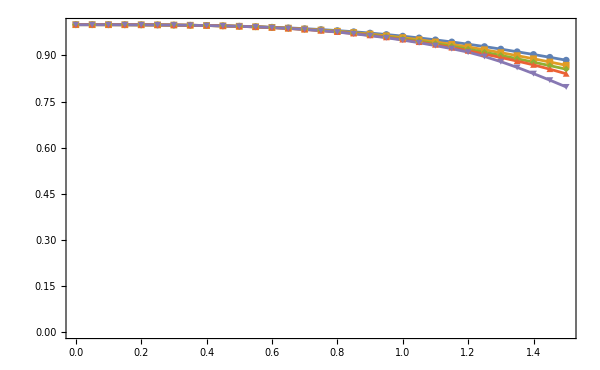

```mathematica
ListPlot[{Fα81,Fα91,Fα101,Fα111,Fα121},PlotLegends->{MaTeX @ "n = 8",MaTeX @ "n = 9", MaTeX @ "n = 10",MaTeX @ "n = 11",MaTeX @ "n = 12"}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},ImageSize->600]
```

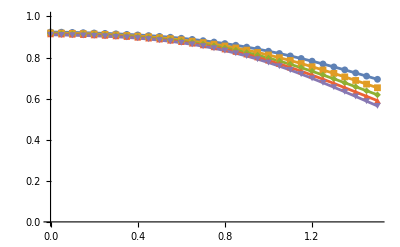

```mathematica
ListPlot[{Fα82,Fα92,Fα102,Fα112,Fα122},PlotLegends->{MaTeX @ "n = 8",MaTeX @ "n = 9", MaTeX @ "n = 10",MaTeX @ "n = 11",MaTeX @ "n = 12"}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1}]
```

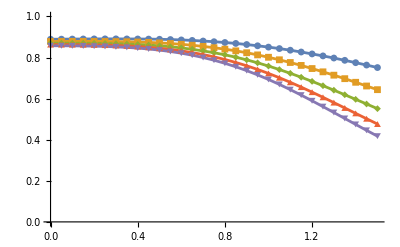

```mathematica
ListPlot[{Fα83,Fα93,Fα103,Fα113,Fα123},PlotLegends->{MaTeX @ "n = 8",MaTeX @ "n = 9", MaTeX @ "n = 10",MaTeX @ "n = 11",MaTeX @ "n = 12"}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1}]
```

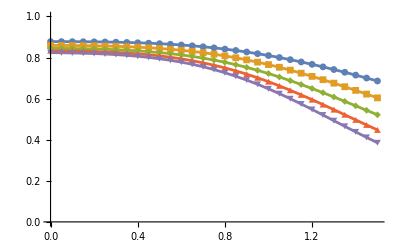

```mathematica
ListPlot[{Fα84,Fα94,Fα104,Fα114,Fα124 },PlotLegends->{MaTeX @ "n = 8",MaTeX @ "n = 9", MaTeX @ "n = 10",MaTeX @ "n = 11",MaTeX @ "n = 12"}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1}]
```

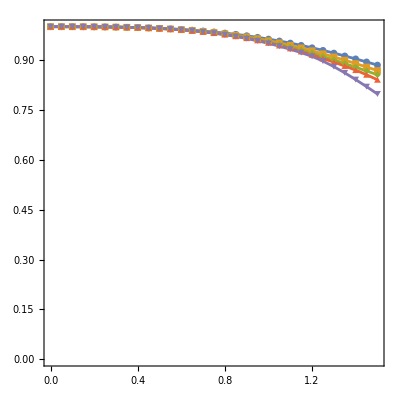

```mathematica
ListPlot[{Fα81,Fα91,Fα101,Fα111,Fα121},PlotLegends->Placed[{MaTeX @ "n = 8",MaTeX @ "n = 9", MaTeX @ "n = 10",MaTeX @ "n = 11",MaTeX @ "n = 12"},{0.21,0.42}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

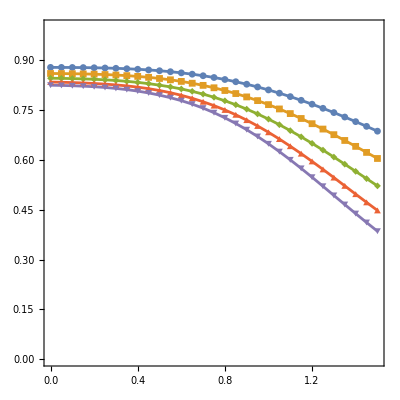

```mathematica
ListPlot[{Fα84,Fα94,Fα104,Fα114,Fα124},PlotLegends->Placed[{MaTeX @ "n = 8",MaTeX @ "n = 9", MaTeX @ "n = 10",MaTeX @ "n = 11",MaTeX @ "n = 12"},{0.21,0.42}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

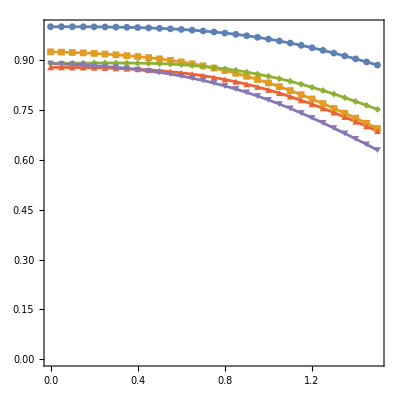

```mathematica
ListPlot[{Fα81,Fα82,Fα83,Fα84, Fα85},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

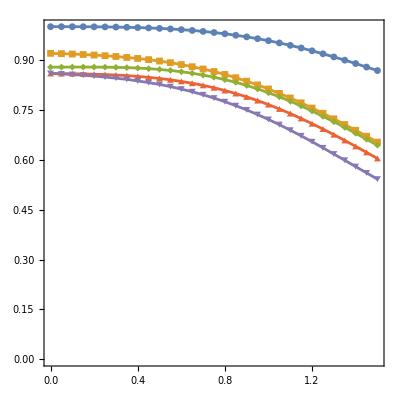

```mathematica
ListPlot[{Fα91,Fα92,Fα93,Fα94, Fα95},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

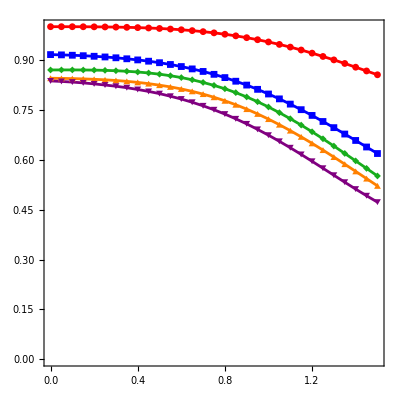

```mathematica
ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

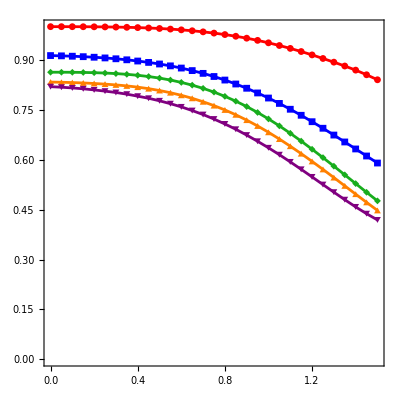

```mathematica
ListPlot[{Fα111,Fα112,Fα113,Fα114, Fα115},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

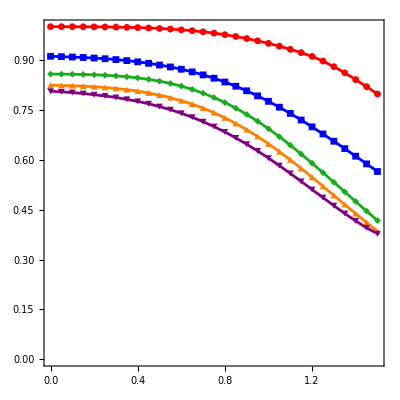

```mathematica
ListPlot[{Fα121,Fα122,Fα123,Fα124, Fα125},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

```mathematica
Fα122
```

{{0.,0.9108},{0.05,0.909823},{0.1,0.908634},{0.15,0.907306},{0.2,0.905645},{0.25,0.903583},{0.3,0.90105},{0.35,0.897962},{0.4,0.89423},{0.45,0.889758},{0.5,0.884706},{0.55,0.878889},{0.6,0.872045},{0.65,0.864064},{0.7,0.855032},{0.75,0.845045},{0.8,0.833656},{0.85,0.820918},{0.9,0.807183},{0.95,0.791904},{1.,0.775543},{1.05,0.757895},{1.1,0.739169},{1.15,0.719386},{1.2,0.698828},{1.25,0.677384},{1.3,0.65558},{1.35,0.633364},{1.4,0.610925},{1.45,0.588488},{1.5,0.566247}}

```mathematica
MapAt[#/4&,Fα122,{All,2}]
```

{{0.,0.2277},{0.05,0.227456},{0.1,0.227158},{0.15,0.226827},{0.2,0.226411},{0.25,0.225896},{0.3,0.225262},{0.35,0.22449},{0.4,0.223557},{0.45,0.22244},{0.5,0.221176},{0.55,0.219722},{0.6,0.218011},{0.65,0.216016},{0.7,0.213758},{0.75,0.211261},{0.8,0.208414},{0.85,0.20523},{0.9,0.201796},{0.95,0.197976},{1.,0.193886},{1.05,0.189474},{1.1,0.184792},{1.15,0.179846},{1.2,0.174707},{1.25,0.169346},{1.3,0.163895},{1.35,0.158341},{1.4,0.152731},{1.45,0.147122},{1.5,0.141562}}

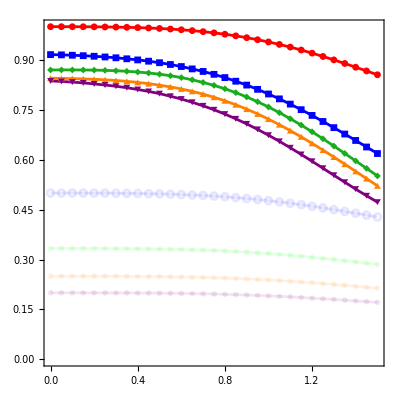

```mathematica
ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105,MapAt[#/2&,Fα101,{All,2}],MapAt[#/3&,Fα101,{All,2}],MapAt[#/4&,Fα101,{All,2}], MapAt[#/5&,Fα101,{All,2}]},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

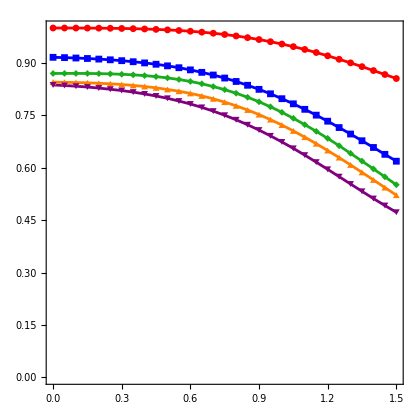

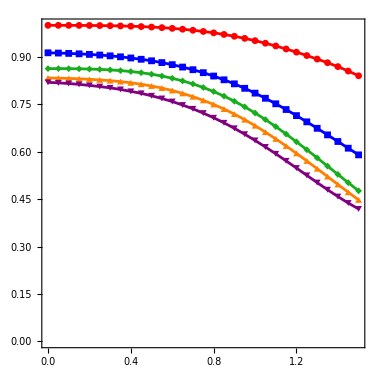

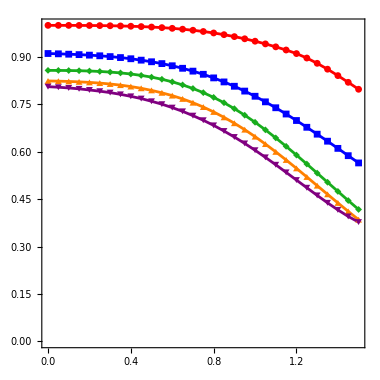

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_10.pdf

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_11.pdf

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_12.pdf

```mathematica
plt10 = ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1,ImageSize->420]
plt11 = ListPlot[{Fα111,Fα112,Fα113,Fα114, Fα115}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha"},AspectRatio->1,ImageSize->380]
plt12=ListPlot[{Fα121,Fα122,Fα123,Fα124, Fα125},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.2,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha"},AspectRatio->1,ImageSize->380]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_10.pdf",plt10]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_11.pdf",plt11]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_12.pdf",plt12]
```

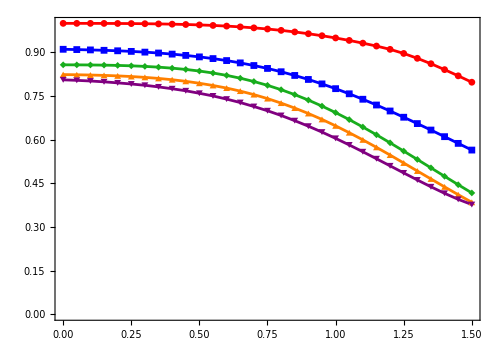

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_12_column.pdf

```mathematica
plt12=ListPlot[{Fα121,Fα122,Fα123,Fα124, Fα125},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.14,0.3}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,DarkGreen,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha", "F^{(k)}(t)"},AspectRatio->0.7,ImageSize->500]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_12_column.pdf",plt12]
```

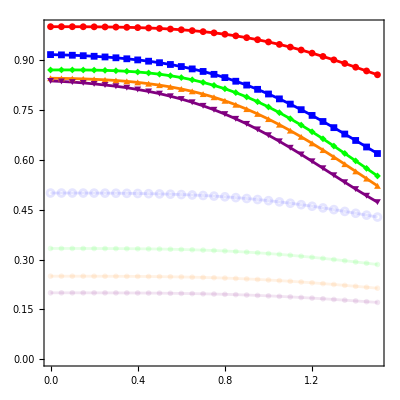

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_10.pdf

```mathematica
plt = ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105,MapAt[#/2&,Fα101,{All,2}],MapAt[#/3&,Fα101,{All,2}],MapAt[#/4&,Fα101,{All,2}], MapAt[#/5&,Fα101,{All,2}]}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,Green,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_10.pdf",plt]
```

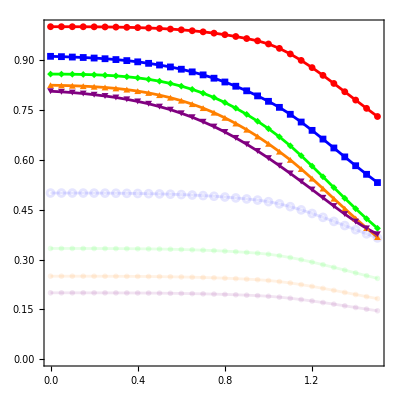

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_12.pdf

```mathematica
plt=ListPlot[{Fα121,Fα122,Fα123,Fα124, Fα125,MapAt[#/2&,Fα121,{All,2}],MapAt[#/3&,Fα121,{All,2}],MapAt[#/4&,Fα121,{All,2}], MapAt[#/5&,Fα121,{All,2}]},PlotLegends->{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"}, Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,Green,Orange,Purple,
Directive[Blue, Opacity[0.1]],
Directive[Green, Opacity[0.1]],
Directive[Orange, Opacity[0.1]],
Directive[Purple, Opacity[0.1]]},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha",""},AspectRatio->1]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_fidelities_for_k_up_to_5_n_12.pdf",plt]
```

```mathematica
Options[plotGrid]={ImagePadding->34};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

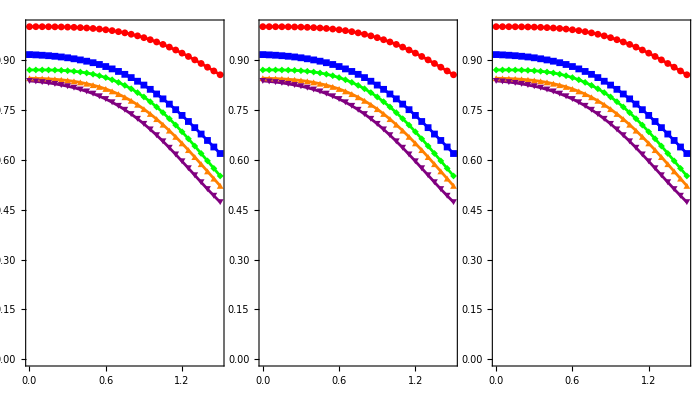

```mathematica
pltgrid = plotGrid[{{
ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,Green,Orange,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1],
ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,Green,Orange,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1],
ListPlot[{Fα101,Fα102,Fα103,Fα104, Fα105},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.38}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},PlotStyle-> {Red,Blue,Green,Orange,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]}},700,400];
pltgrid
```

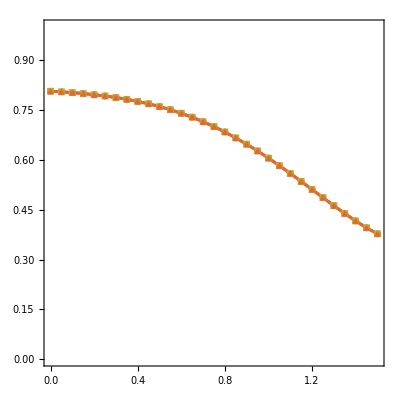

```mathematica
ListPlot[{Fα125,Fα125,Fα125,Fα125},PlotLegends->Placed[{MaTeX @ "k = 1",MaTeX @ "k = 2", MaTeX @ "k = 3",MaTeX @ "k = 4", MaTeX @ "k = 5"},{0.21,0.42}], Joined->True,PlotMarkers->{Automatic,7},PlotRange->{0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\alpha","F^{(k)}(t)"},AspectRatio->1]
```

```mathematica
FindMaxγ[8,2,0.1]
```

General::munfl: (-1.96527×10^-157+0. ⅈ) (0.+3.19169×10^-154 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.96527×10^-157+0. ⅈ) (-9.55973×10^-153+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.96527×10^-157+0. ⅈ) (0.-9.54441×10^-152 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

General::stop: Further output of Eigenvalues::eival will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.134265,0.919303}

{0.134265,0.919303}

```mathematica
FindMaxγ[8,2,0.2]
```

$Aborted

```mathematica
Table[FindMaxγ[8,2,α],{α,0,1.0,0.1}]
```

$Aborted

```mathematica
Table[FindMaxγ[10,2,α],{α,0,1.0,0.1}]
```

```mathematica
Table[FindMaxγ[8,3,α],{α,0,1.0,0.1}]
```

```mathematica
Table[FindMaxγ[10,3,α] ,{α,0,1.0,0.1}]
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

$Aborted

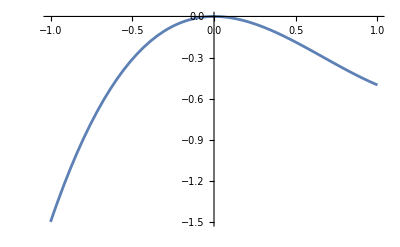

```mathematica
Plot[max[γ],{γ,-1,1}]
```

```mathematica
reg = Interval[{-1,1} ]
max[γ_]:=0.5 γ^3-γ^2
```

Interval[{-1,1}]

```mathematica
BayesianMaximization[max,reg,AssumeDeterministic -> True, MaxIterations->50]
```

BayesianMaximizationObject[…]

```mathematica
FindMaximum[max[γ],{γ,-1}]
```

{-4.91125×10^-21,{γ→-7.00803×10^-11}}

```mathematica
Hs[n_] := {{0,√2 √(-2+n),0},{√2 √(-2+n),-2+n,2 √(-3+n)},{0,2 √(-3+n),2 (-4+n)}}
```

```mathematica
Binomial[n-2,3-1]-1+(3-1)
```

1+1/2 (-3+n) (-2+n)

```mathematica
HsearchTotal[n,3,γ] // FullSimplify// MatrixForm
```

(3/2 | √3 √(-3+n) γ | 0 | 0
√3 √(-3+n) γ | 1/2+(-2+n) γ | 2 √2 √(-4+n) γ | 0
0 | 2 √2 √(-4+n) γ | -1/2+2 (-4+n) γ | 3 √(-5+n) γ
0 | 0 | 3 √(-5+n) γ | -3/2+3 (-6+n) γ)

```mathematica
Hsearch[n,4]// FullSimplify // MatrixForm
```

(0 | 2 √(-4+n) | 0 | 0 | 0
2 √(-4+n) | -2+n | 2 √3 √(-5+n) | 0 | 0
0 | 2 √3 √(-5+n) | 2 (-4+n) | 3 √2 √(-6+n) | 0
0 | 0 | 3 √2 √(-6+n) | 3 (-6+n) | 4 √(-7+n)
0 | 0 | 0 | 4 √(-7+n) | 4 (-8+n))

```mathematica
Series[HsearchTotal[n,3,γ],{n,∞,1}] // FullSimplify // MatrixForm
```

(3/2 | √3 γ √n-3/2 (√3 γ) √(1/n)+O[1/n]^(3/2) | 0 | 0
√3 γ √n-3/2 (√3 γ) √(1/n)+O[1/n]^(3/2) | γ n+(1/2-2 γ)+O[1/n]^2 | 2 √2 γ √n-4 (√2 γ) √(1/n)+O[1/n]^(3/2) | 0
0 | 2 √2 γ √n-4 (√2 γ) √(1/n)+O[1/n]^(3/2) | 2 γ n+(-1/2-8 γ)+O[1/n]^2 | 3 γ √n-15/2 γ √(1/n)+O[1/n]^(3/2)
0 | 0 | 3 γ √n-15/2 γ √(1/n)+O[1/n]^(3/2) | 3 γ n+(-3/2-18 γ)+O[1/n]^2)

```mathematica
Series[HsearchTotal[n,3,1/n],{n,∞,1}] // FullSimplify // MatrixForm
```

(3/2 | √3 √(1/n)+O[1/n]^(3/2) | 0 | 0
√3 √(1/n)+O[1/n]^(3/2) | 3/2-2/n+O[1/n]^2 | 2 √2 √(1/n)+O[1/n]^(3/2) | 0
0 | 2 √2 √(1/n)+O[1/n]^(3/2) | 3/2-8/n+O[1/n]^2 | 3 √(1/n)+O[1/n]^(3/2)
0 | 0 | 3 √(1/n)+O[1/n]^(3/2) | 3/2-18/n+O[1/n]^2)

```mathematica
m2 = {{0,√2,0},{√2,0,2},{0,2,0}};
m3 = {{0,√3,0,0},{√3,0,2 √2,0},{0,2 √2,0,3},{0,0,3,0}};
```

```mathematica
MatrixExp[- I m2 t] //FullSimplify// MatrixForm
```

(1/3 (2+Cos[√6 t]) | -(ⅈ Sin[√6 t])/(√3) | 1/3 √2 (-1+Cos[√6 t])
-(ⅈ Sin[√6 t])/(√3) | Cos[√6 t] | -ⅈ √(2/3) Sin[√6 t]
1/3 √2 (-1+Cos[√6 t]) | -ⅈ √(2/3) Sin[√6 t] | 1/3 (1+2 Cos[√6 t]))

```mathematica
With[{t=1/Sqrt[10-√73] Pi/2},MatrixExp[- I m3 t]]// FullSimplify // MatrixForm
```

(-1/292 (-73+7 √73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)) | 1/2 √(3/146) (-2 ⅈ √(11+√73)-√(11-√73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (-1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.))) | √(3/146) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)) | ⅈ √(2/73) (√(10+√73)-√(10-√73) Sin[√(173/108+(5 √73)/27) π])
1/2 √(3/146) (-2 ⅈ √(11+√73)-√(11-√73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (-1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.))) | 1/292 (73+√73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)) | (2 ⅈ (-73+10 √73)-3 √219 ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (-1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)))/(73 √(20-2 √73)) | (3 ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)))/(√146)
√(3/146) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)) | (2 ⅈ (-73+10 √73)-3 √219 ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (-1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)))/(73 √(20-2 √73)) | 1/292 (73+7 √73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)) | 1/2 √(3/146) (-√(11+√73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (-1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.))+Root-3.13 ⅈRoot[768+88 #1^2+#1^4&,1]0.)
ⅈ √(2/73) (√(10+√73)-√(10-√73) Sin[√(173/108+(5 √73)/27) π]) | (3 ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)))/(√146) | 1/2 √(3/146) (-√(11+√73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (-1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.))+Root-3.13 ⅈRoot[768+88 #1^2+#1^4&,1]0.) | -1/292 (-73+√73) ⅇ^(π Root-1.78 ⅈRoot[27+1384 #1^2+432 #1^4&,3]0.) (1+ⅇ^(π Root3.57 ⅈRoot[27+346 #1^2+27 #1^4&,4]0.)))

```mathematica
MatrixPower[m2,6]
```

{{8,0,56 √2},{0,8,112},{0,0,64}}

```mathematica
Normal[Series[HsearchTotal[n,3,1/n],{n,∞,1}]] // FullSimplify // MatrixForm
```

(3/2 | (√3)/(√n) | 0 | 0
(√3)/(√n) | 3/2-2/n | (2 √2)/(√n) | 0
0 | (2 √2)/(√n) | 3/2-8/n | 3/(√n)
0 | 0 | 3/(√n) | 3/2-18/n)

```mathematica
Abs[ markedVec[3].MatrixExp[I Normal[Series[HsearchTotal[n,3,1/n],{n,∞,1}]] t].superpositionVec[n,3]]^2
```

(Abs[-1/(√((-2+n) (-1+n) n))6144 √6 √((-5+n) (-4+n) (-3+n)) n^9 RootSum[-56623104 n^11+54263808 n^12-9142272 n^13+331776 n^14+1179648 n^(15/2) #1-3391488 n^(17/2) #1+1019904 n^(19/2) #1-55296 n^(21/2) #1+50176 n^5 #1^2-37376 n^6 #1^2+3456 n^7 #1^2+448 n^(5/2) #1^3-96 n^(7/2) #1^3+#1^4&,ⅇ^((ⅈ t #1)/(16 n^(7/2)))/(-294912 n^(15/2)+847872 n^(17/2)-254976 n^(19/2)+13824 n^(21/2)-25088 n^5 #1+18688 n^6 #1-1728 n^7 #1-336 n^(5/2) #1^2+72 n^(7/2) #1^2-#1^3)&]+1/(√((-2+n) (-1+n) n))384 √2 √((-4+n) (-3+n)) RootSum[-56623104 n^11+54263808 n^12-9142272 n^13+331776 n^14+1179648 n^(15/2) #1-3391488 n^(17/2) #1+1019904 n^(19/2) #1-55296 n^(21/2) #1+50176 n^5 #1^2-37376 n^6 #1^2+3456 n^7 #1^2+448 n^(5/2) #1^3-96 n^(7/2) #1^3+#1^4&,(-288 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(17/2)+24 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(19/2)-√3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^6 #1)/(-294912 n^(15/2)+847872 n^(17/2)-254976 n^(19/2)+13824 n^(21/2)-25088 n^5 #1+18688 n^6 #1-1728 n^7 #1-336 n^(5/2) #1^2+72 n^(7/2) #1^2-#1^3)&]-1/(√((-2+n) (-1+n) n))12 √2 √(-3+n) RootSum[-56623104 n^11+54263808 n^12-9142272 n^13+331776 n^14+1179648 n^(15/2) #1-3391488 n^(17/2) #1+1019904 n^(19/2) #1-55296 n^(21/2) #1+50176 n^5 #1^2-37376 n^6 #1^2+3456 n^7 #1^2+448 n^(5/2) #1^3-96 n^(7/2) #1^3+#1^4&,(36864 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^8-12288 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^9+576 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^10+416 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(11/2) #1-48 √3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(13/2) #1+√3 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^3 #1^2)/(-294912 n^(15/2)+847872 n^(17/2)-254976 n^(19/2)+13824 n^(21/2)-25088 n^5 #1+18688 n^6 #1-1728 n^7 #1-336 n^(5/2) #1^2+72 n^(7/2) #1^2-#1^3)&]+1/(2 √((-2+n) (-1+n) n))√(3/2) RootSum[-56623104 n^11+54263808 n^12-9142272 n^13+331776 n^14+1179648 n^(15/2) #1-3391488 n^(17/2) #1+1019904 n^(19/2) #1-55296 n^(21/2) #1+50176 n^5 #1^2-37376 n^6 #1^2+3456 n^7 #1^2+448 n^(5/2) #1^3-96 n^(7/2) #1^3+#1^4&,(-1179648 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(15/2)+1867776 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(17/2)-362496 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(19/2)+13824 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(21/2)-50176 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^5 #1+25856 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^6 #1-1728 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^7 #1-448 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(5/2) #1^2+72 ⅇ^((ⅈ t #1)/(16 n^(7/2))) n^(7/2) #1^2-ⅇ^((ⅈ t #1)/(16 n^(7/2))) #1^3)/(-294912 n^(15/2)+847872 n^(17/2)-254976 n^(19/2)+13824 n^(21/2)-25088 n^5 #1+18688 n^6 #1-1728 n^7 #1-336 n^(5/2) #1^2+72 n^(7/2) #1^2-#1^3)&]])^2

```mathematica
asd √df// FullSimplify
```

((-1+s) s)/(-3+s)^3

```mathematica
HsearchTotal[n,2,γ] // MatrixForm
```

(1+2 γ | √2 √(-2+n) γ | 0
√2 √(-2+n) γ | (-2+n) γ | 2 √(-3+n) γ
0 | 2 √(-3+n) γ | -1+2 (-4+n) γ)

```mathematica
FidA[nbits_,γ_,t_] :=Abs[ markedVec[2].MatrixExp[I (γ Hs[nbits] + Hmarked[2]) t].superpositionVec[nbits,2]]^2
```

```mathematica
Clear[k,γ]
```

0.999904

5.

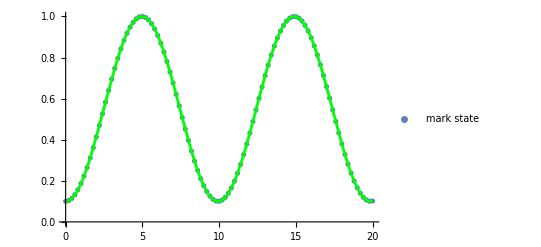

```mathematica
nbits = 10;
k= 1;
tmax= 20;
γ = N[1/(nbits-2)];
γ = 0.1;
fids = Fidelities[nbits,k,γ,tmax];
maxfidelity=Max[fids[[All,2]]]
time = fids[[All,1]][[Ordering[fids[[All,2]],-1][[1]]]]
pltn14 = ListPlot[fids,PlotLegends->{"mark state"}, PlotRange->{0,1}];
plta14 = Plot[FidelityAnalytical[nbits,k,γ,t],{t,0,tmax}, PlotStyle->Green, PlotRange->{0,1}];
Show[pltn14, plta14]
```

```mathematica
Clear[fidsA]
```

```mathematica
<< MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->18};
SetOptions[MaTeX,"FontSize"->18,"Magnification"->1.2];
```

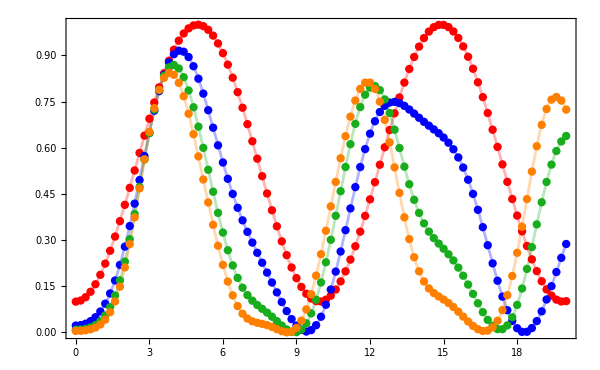

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_k_subspaces.pdf

```mathematica
nbits = 10;
tmax= 20;
γ = 0.1;
fids = Table[Fidelities[nbits,k,γ,tmax],{k,1,4}];
fidsA[t_] := Table[{FidelityAnalytical[nbits,k,γ,t]},{k,1,4}];
plt = ListPlot[fids, PlotStyle-> {{Red, PointSize[0.01]},{Blue,PointSize[0.01]},{DarkGreen, PointSize[0.01]},{Orange, PointSize[0.01]}}, PlotLegends->{MaTeX @ "k=1",MaTeX @"k=2",MaTeX @"k=3",MaTeX @"k=4"},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"t","F^{(k)}"}];
pltA1 = Plot[FidelityAnalytical[nbits,1,γ,t],{t,0,tmax},PlotStyle->{Red, Opacity[0.3]}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"t","F^{(k)}"}];
pltA2 = Plot[FidelityAnalytical[nbits,2,γ,t],{t,0,tmax},PlotStyle->{Blue, Opacity[0.3],BaseStyle->texStyle}, PlotRange->{0,1},FrameLabel -> MaTeX @ {"t","F^{(k)}"}];
pltA3 = Plot[FidelityAnalytical[nbits,3,γ,t],{t,0,tmax},PlotStyle->{DarkGreen, Opacity[0.3]}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"t","F^{(k)}"}];
pltA4 = Plot[FidelityAnalytical[nbits,4,γ,t],{t,0,tmax},PlotStyle->{Orange, Opacity[0.3]}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"t","F^{(k)}"}];
pltks=Show[pltA1,pltA2,pltA3,pltA4,plt,PlotRange-> {0,1},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"t","F^{(k)}(t)"},ImageSize->600]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_k_subspaces.pdf",pltks]
```

```mathematica
FindMaxFt[k0_]:= Module[{k=k0}, 
Hinf = N[Table[Table[If[Abs[j-i]==1,Min[i,j]Sqrt[(k+1-Min[i,j])],0],{i,1,k+1}],{j,1,k+1}]];
MatExp[t_]=N[MatrixExp[I Hinf t]];
Fid[t_]:= Abs[ UnitVector[k+1,1].MatExp[t]. UnitVector[k+1,k+1]]^2;
max = FindMaximum[Fid[t],{t,0.25}];
{max[[1]],t /. max[[2]]}
]
```

```mathematica
FindMax[k0_]:= Module[{k=k0}, 
Hinf = N[Table[Table[If[Abs[j-i]==1,Min[i,j]Sqrt[(k+1-Min[i,j])],0],{i,1,k+1}],{j,1,k+1}]];
MatExp[t_]=N[MatrixExp[I Hinf t]];
Fid[t_]:= Abs[ UnitVector[k+1,1].MatExp[t]. UnitVector[k+1,k+1]]^2;
max = FindMaximum[Fid[t],{t,0.25}];
{t /. max[[2]],max[[1]]}
]
```

```mathematica
t /. FindMaximum[FidelityAsymptotic[2,t],{t,1}]
```

ReplaceAll::rmix: Elements of {0.888889,{t→1.28255}} are a mixture of lists and nonlists.

t/.{0.888889,{t→1.28255}}

```mathematica
FindMax[16]
```

{0.42993,0.690351}

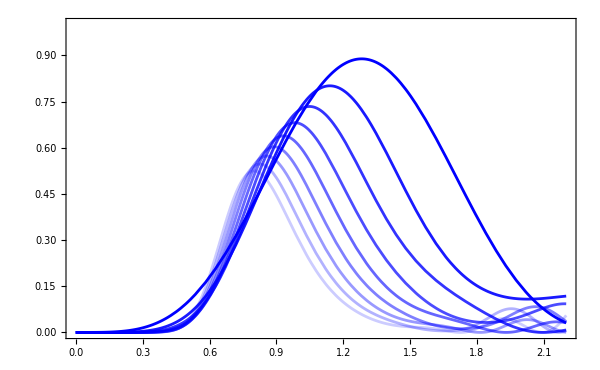

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_k_fidelities_asymptotic.pdf

```mathematica
tmax= 2.2;
plt = Plot[{FidelityAsymptotic[2,t],FidelityAsymptotic[3,t],FidelityAsymptotic[4,t],FidelityAsymptotic[5,t],FidelityAsymptotic[6,t],FidelityAsymptotic[7,t],FidelityAsymptotic[8,t],FidelityAsymptotic[9,t],FidelityAsymptotic[10,t]},{t,0,tmax}, PlotLegends->{MaTeX @ "k=2",MaTeX @"k=3",MaTeX @"k=4",MaTeX @"k=5",MaTeX @"k=6",MaTeX @"k=7",MaTeX @"k=8",MaTeX @"k=9",MaTeX @"k=10" },PlotStyle->{{Blue,Opacity[1]},{Blue,Opacity[0.9]},{Blue,Opacity[0.8]},{Blue,Opacity[0.7]},{Blue,Opacity[0.6]},{Blue,Opacity[0.5]},{Blue,Opacity[0.4]},{Blue,Opacity[0.3]},{Blue,Opacity[0.2]}}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"}];
pltks=Show[plt,BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"},ImageSize->600]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_k_fidelities_asymptotic.pdf",pltks]
```

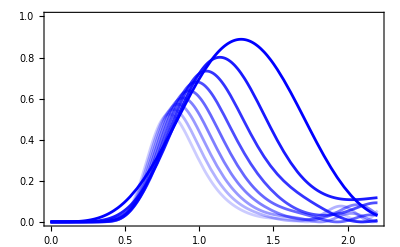

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_k_fidelities_asymptotic_column.pdf

```mathematica
tmax= 2.2;
plt = Plot[{FidelityAsymptotic[2,t],FidelityAsymptotic[3,t],FidelityAsymptotic[4,t],FidelityAsymptotic[5,t],FidelityAsymptotic[6,t],FidelityAsymptotic[7,t],FidelityAsymptotic[8,t],FidelityAsymptotic[9,t],FidelityAsymptotic[10,t]},{t,0,tmax}, PlotLegends->{MaTeX @ "k=2",MaTeX @"k=3",MaTeX @"k=4",MaTeX @"k=5",MaTeX @"k=6",MaTeX @"k=7",MaTeX @"k=8",MaTeX @"k=9",MaTeX @"k=10" },PlotStyle->{{Blue,Opacity[1]},{Blue,Opacity[0.9]},{Blue,Opacity[0.8]},{Blue,Opacity[0.7]},{Blue,Opacity[0.6]},{Blue,Opacity[0.5]},{Blue,Opacity[0.4]},{Blue,Opacity[0.3]},{Blue,Opacity[0.2]}}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"}];
pltks=Show[plt,BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"},ImageSize->400]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_k_fidelities_asymptotic_column.pdf",pltks]
```

```mathematica
Table[{k,FindMax[k][[2]]},{k,1,100,1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{1,1.},{2,0.888889},{3,0.801226},{4,0.734109},{5,0.681372},{6,0.638661},{7,0.60316},{8,0.573033},{9,0.54704},{10,0.52431},{11,0.504212},{12,0.486271},{13,0.470127},{14,0.455497},{15,0.442158},{16,0.42993},{17,0.418667},{18,0.408247},{19,0.398571},{20,0.389554},{21,0.381123},{22,0.373219},{23,0.365788},{24,0.358785},{25,0.35217},{26,0.345908},{27,0.33997},{28,0.334328},{29,0.328958},{30,0.323839},{31,0.318952},{32,0.314281},{33,0.309809},{34,0.305523},{35,0.30141},{36,0.29746},{37,0.29366},{38,0.290003},{39,0.28648},{40,0.283081},{41,0.279802},{42,0.276633},{43,0.27357},{44,0.270607},{45,0.267738},{46,0.264958},{47,0.262264},{48,0.25965},{49,0.257112},{50,0.254648},{51,0.252253},{52,0.249925},{53,0.24766},{54,0.245455},{55,0.243308},{56,0.241217},{57,0.239179},{58,0.237192},{59,0.235253},{60,0.233361},{61,0.231514},{62,0.229711},{63,0.227948},{64,0.226226},{65,0.224542},{66,0.222896},{67,0.221285},{68,0.219708},{69,0.218165},{70,0.216654},{71,0.215174},{72,0.213724},{73,0.212302},{74,0.210909},{75,0.209543},{76,0.208203},{77,0.206888},{78,0.205598},{79,0.204332},{80,0.203089},{81,0.201868},{82,0.200669},{83,0.199492},{84,0.198334},{85,0.197197},{86,0.196079},{87,0.19498},{88,0.193899},{89,0.192836},{90,0.19179},{91,0.190761},{92,0.189749},{93,0.188752},{94,0.187771},{95,0.186805},{96,0.185854},{97,0.184917},{98,0.183994},{99,0.183085},{100,0.182189}}

```mathematica
Table[{k,FindMax[k][[2]]},{k,101,150,1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{101,0.181307},{102,0.180437},{103,0.179579},{104,0.178734},{105,0.1779},{106,0.177078},{107,0.176267},{108,0.175467},{109,0.174678},{110,0.1739},{111,0.173132},{112,0.172374},{113,0.171626},{114,0.170887},{115,0.170158},{116,0.169439},{117,0.168728},{118,0.168026},{119,0.167333},{120,0.166648},{121,0.165972},{122,0.165304},{123,0.164644},{124,0.163991},{125,0.163347},{126,0.16271},{127,0.16208},{128,0.161458},{129,0.160842},{130,0.160234},{131,0.159633},{132,0.159038},{133,0.15845},{134,0.157868},{135,0.157293},{136,0.156724},{137,0.156161},{138,0.155604},{139,0.155053},{140,0.154508},{141,0.153969},{142,0.153435},{143,0.152906},{144,0.152384},{145,0.151866},{146,0.151354},{147,0.150846},{148,0.150344},{149,0.149847},{150,0.149355}}

```mathematica
Table[FindMax[k],{k,1,100,1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{1.5708,1.},{1.28255,0.888889},{1.13972,0.801226},{1.04866,0.734109},{0.982992,0.681372},{0.932026,0.638661},{0.890561,0.60316},{0.855747,0.573033},{0.825853,0.54704},{0.799744,0.52431},{0.776631,0.504212},{0.755947,0.486271},{0.737267,0.470127},{0.720268,0.455497},{0.704697,0.442158},{0.690351,0.42993},{0.67707,0.418667},{0.664721,0.408247},{0.653191,0.398571},{0.642391,0.389554},{0.632241,0.381123},{0.622675,0.373219},{0.613636,0.365788},{0.605075,0.358785},{0.596949,0.35217},{0.58922,0.345908},{0.581855,0.33997},{0.574825,0.334328},{0.568103,0.328958},{0.561667,0.323839},{0.555497,0.318952},{0.549572,0.314281},{0.543877,0.309809},{0.538396,0.305523},{0.533116,0.30141},{0.528023,0.29746},{0.523107,0.29366},{0.518357,0.290003},{0.513763,0.28648},{0.509317,0.283081},{0.50501,0.279802},{0.500835,0.276633},{0.496785,0.27357},{0.492853,0.270607},{0.489035,0.267738},{0.485323,0.264958},{0.481713,0.262264},{0.4782,0.25965},{0.474779,0.257112},{0.471448,0.254648},{0.4682,0.252253},{0.465033,0.249925},{0.461944,0.24766},{0.458929,0.245455},{0.455984,0.243308},{0.453108,0.241217},{0.450298,0.239179},{0.44755,0.237192},{0.444862,0.235253},{0.442233,0.233361},{0.43966,0.231514},{0.437141,0.229711},{0.434673,0.227948},{0.432256,0.226226},{0.429887,0.224542},{0.427565,0.222896},{0.425288,0.221285},{0.423055,0.219708},{0.420864,0.218165},{0.418713,0.216654},{0.416602,0.215174},{0.41453,0.213724},{0.412494,0.212302},{0.410495,0.210909},{0.40853,0.209543},{0.406599,0.208203},{0.4047,0.206888},{0.402834,0.205598},{0.400998,0.204332},{0.399193,0.203089},{0.397416,0.201868},{0.395668,0.200669},{0.393948,0.199492},{0.392254,0.198334},{0.390586,0.197197},{0.388944,0.196079},{0.387327,0.19498},{0.385734,0.193899},{0.384164,0.192836},{0.382617,0.19179},{0.381092,0.190761},{0.379589,0.189749},{0.378107,0.188752},{0.376646,0.187771},{0.375206,0.186805},{0.373785,0.185854},{0.372383,0.184917},{0.371,0.183994},{0.369635,0.183085},{0.368288,0.182189}}

```mathematica
Table[FindMax[k],{k,101,150,1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{0.366959,0.181307},{0.365647,0.180437},{0.364352,0.179579},{0.363073,0.178734},{0.36181,0.1779},{0.360563,0.177078},{0.359331,0.176267},{0.358114,0.175467},{0.356912,0.174678},{0.355725,0.1739},{0.354551,0.173132},{0.353391,0.172374},{0.352245,0.171626},{0.351112,0.170887},{0.349992,0.170158},{0.348885,0.169439},{0.34779,0.168728},{0.346708,0.168026},{0.345638,0.167333},{0.344579,0.166648},{0.343532,0.165972},{0.342496,0.165304},{0.341471,0.164644},{0.340458,0.163991},{0.339455,0.163347},{0.338462,0.16271},{0.33748,0.16208},{0.336508,0.161458},{0.335546,0.160842},{0.334594,0.160234},{0.333651,0.159633},{0.332718,0.159038},{0.331794,0.15845},{0.330879,0.157868},{0.329974,0.157293},{0.329077,0.156724},{0.328188,0.156161},{0.327309,0.155604},{0.326437,0.155053},{0.325574,0.154508},{0.324719,0.153969},{0.323872,0.153435},{0.323033,0.152906},{0.322201,0.152384},{0.321378,0.151866},{0.320561,0.151354},{0.319752,0.150846},{0.318951,0.150344},{0.318156,0.149847},{0.317368,0.149355}}

```mathematica
tF150 = {{1.570796315295842,0.9999999999999996},{1.2825498192855294,0.8888888888888885},{1.1397196797298803,0.8012263810222657},{1.0486560431781162,0.734109105839151},{0.9829924595550299,0.681372020154753},{0.9320258506555367,0.6386613705526571},{0.8905610646082863,0.6031602888592883},{0.8557469269481319,0.5730328592001143},{0.8258529305314967,0.5470396675485579},{0.7997435671319791,0.5243101592180128},{0.7766311823949386,0.5042115299779354},{0.7559469987676953,0.4862708562702818},{0.7372672642981934,0.4701265310003641},{0.7202680866447779,0.45549664334150636},{0.7046965394747949,0.44215769583475323},{0.6903514921778766,0.42992988687451034},{0.6770704928169223,0.4186666911359205},{0.6647205252903602,0.40824732773061534},{0.6531914104470454,0.39857121455855227},{0.642390875459856,0.38955381759459984},{0.632240929974311,0.38112349821606},{0.6226751291274716,0.37321908660041503},{0.6136363864026105,0.365787991355977},{0.6050753432486795,0.35878471064353196},{0.5969490412034636,0.3521696476845395},{0.589219887113973,0.3459081596948952},{0.581854800878985,0.33996978772208625},{0.5748245330410003,0.33432762805120025},{0.5681031029650971,0.3289578153999319},{0.5616673430080324,0.3238390951283667},{0.5554965105881222,0.318952466882763},{0.5495719342809733,0.3142808859832216},{0.5438768271012099,0.3098090118071578},{0.5383959691055744,0.3055229946658185},{0.5331155607290425,0.3014102943986995},{0.5280230430429411,0.29745952525146535},{0.523106959990758,0.2936603226497024},{0.5183568401870676,0.2900032283056733},{0.5137630514787697,0.2864795907478173},{0.5093167939415947,0.2830814788834697},{0.5050099313698163,0.2798016066225007},{0.5008349526654816,0.27663326692661677},{0.4967849380070449,0.2735702739215558},{0.4928534518698483,0.27060691193203146},{0.4890345454503534,0.26773789048146157},{0.4853226760090379,0.2649583044483971},{0.4817126870127876,0.26226359869504573},{0.4781997741978149,0.2596495365865771},{0.4747794505901599,0.25711217190483254},{0.4714475173755252,0.25464782373236644},{0.46820004929952613,0.25225305394220754},{0.46503336193334044,0.24992464697972788},{0.461943998161041,0.24765959166571663},{0.45892871023861836,0.24545506478608645},{0.4559844427469981,0.24330841626431585},{0.45310831486722714,0.24121715573947416},{0.4502976133953995,0.2391789403948097},{0.447549775734257,0.23719156390154436},{0.4448623832521153,0.23525294635902871},{0.44223314666094304,0.23336112512678903},{0.43965989200859823,0.23151424645659763},{0.43714057549204327,0.2297105578430735},{0.4346732477155548,0.22794840102133682},{0.432256053484317,0.2262262055476462},{0.42988724950359053,0.2245424829068006},{0.4275651619144562,0.22289582109570072},{0.42528819182538713,0.22128487963852345},{0.4230548464672858,0.21970838499308157},{0.4208636783015128,0.21816512631291635},{0.4187133146726116,0.2166539515328694},{0.41660244636019833,0.21517376374929678},{0.414529822603505,0.2137235178691225},{0.41249424905835125,0.21230221750455813},{0.4104945849442808,0.21090891209216167},{0.40852973688568,0.2095426942177471},{0.40659866155752994,0.20820269712952416},{0.404700360625397,0.20688809242450057},{0.40283386370274,0.20559808789354153},{0.4009982642500079,0.2043319255128392},{0.3991926755813281,0.20308887956996027},{0.3974162522667194,0.2018682549137808},{0.39566818155677097,0.20066938531918557},{0.393947682929354,0.19949163195725395},{0.392254007682565,0.19833438196335407},{0.39058643291449474,0.19719704709559066},{0.3889442654032128,0.19607906247712645},{0.3873268382061311,0.19497988541598976},{0.38573350768127074,0.19389899429714433},{0.3841636550851005,0.19283588754127598},{0.38261668250935144,0.19179008262590125},{0.3810920159770826,0.19076111516426553},{0.3795891000489786,0.18974853803809844},{0.3781074005737248,0.18875192058050863},{0.3766463991247521,0.1877708478056467},{0.3752055976098125,0.18680491968206253},{0.3737845142476942,0.1858537504468099},{0.372382683605467,0.18491696795747323},{0.37099965561692944,0.18399421307998967},{0.3696349952783007,0.18308513910973412},{0.36828828081874554,0.18218941122360063},{0.36695910712154717,0.18130670596166842},{0.36564707725900736,0.18043671073593595},{0.36435181780269416,0.1795791233648626},{0.36307293913967337,0.17873365163219102},{0.3618101033571283,0.1779000128681369},{0.36056295651948495,0.17707793355215257},{0.35933116218378536,0.17626714893562623},{0.3581143974058357,0.1754674026833218},{0.3569123369497869,0.17467844653270845},{0.35572468257749434,0.17390003996999912},{0.3545511340786706,0.17313194992181039},{0.35339140174301714,0.17237395046183235},{0.35224520489690814,0.17162582253149197},{0.3511122710505241,0.17088735367372054},{0.34999233525056134,0.17015833777936595},{0.34888514059979875,0.1694385748454099},{0.3477904364931825,0.16872787074419324},{0.34670797966888,0.16802603700345065},{0.3456375341661148,0.16733289059606743},{0.344578870506044,0.1666482537396117},{0.34353176587370515,0.16597195370450457},{0.34249599903814376,0.16530382263089075},{0.3414713526096741,0.1646436973535091},{0.3404576343218043,0.16399141923425764},{0.3394546341767824,0.16334683400184355},{0.3384621598211965,0.1627097915984806},{0.33748001897947477,0.16208014603309207},{0.33650802650380035,0.1614577552405701},{0.335546001705392,0.1608424809471697},{0.3345937678149516,0.16023418854134605},{0.3336511525817413,0.15963274694988328},{0.33271799419896786,0.15903802851938342},{0.3317941122156765,0.15844990890217173},{0.3308793644852177,0.1578682669471937},{0.32997358868387505,0.15729298459502075},{0.3290766332418514,0.1567239467772142},{0.32818834990036794,0.15616104131946118},{0.32730859430338954,0.1556041588487854},{0.3264372251192154,0.155053192704194},{0.3255741061303517,0.15450803885071088},{0.32471909679566063,0.1539685957970284},{0.3238720709962214,0.15343476451581073},{0.3230328987129357,0.15290644836764347},{0.3222014541582191,0.15238355302720263},{0.3213776144715385,0.151865986412597},{0.3205612618207305,0.15135365861734082},{0.3197522764408611,0.15084648184448862},{0.31895053573744375,0.15034437034354795},{0.31815594039914824,0.14984724034960012},{0.3173683826677837,0.14935501002442889}};
```

```mathematica
ModelExpSimp[a1_,a2_,k_]:=  Exp[-a2 (k-1)]
```

```mathematica
ModelExp[a0_,a1_,a2_,k_]:= a0+a1 Exp[-a2 (k-1)]
```

```mathematica
ModelPoly[a0_,a1_,a2_,k_]:= 1/k^a1
```

```mathematica
ModelExpPoly[a0_,a1_,a2_,a3_,k_]:= a0 k^-a1 Exp[-a2 (k-1)]+a3
```

```mathematica
ModelInverseLog[a0_,a1_,a2_,k_]:= 1/(1+Log[k])
```

```mathematica
FindFit[{0.9999999999999993,0.8888888888888885,0.8012263810222655,0.734109105839151,0.6813720201547535,0.6386613705526571,0.6031602888592889,0.5730328592001142,0.5470396675485575,0.5243101592180128,0.5042115299779353,0.4862708562702815,0.47012653100036444,0.45549664334150625,0.44215769583475306,0.4299298868745107,0.41866669113592075,0.40824732773061645,0.3985712145585518,0.3895538175945986,0.3811234982160593,0.3732190866004154,0.36578799135597795,0.35878471064353157,0.3521696476845407,0.3459081596948954,0.33996978772208586,0.33432762805120037,0.3289578153999316,0.32383909512836734,0.31895246688276274,0.3142808859832215,0.3098090118071572,0.30552299466581934,0.3014102943986997,0.2974595252514656,0.2936603226497019,0.2900032283056719,0.2864795907478174,0.2830814788834712,0.27980160662249903,0.2766332669266169,0.27357027392155475,0.27060691193203296,0.2677378904814604,0.26495830444839613,0.262263598695047,0.2596495365865772,0.25711217190483243,0.25464782373236655,0.252253053942208,0.24992464697972783,0.24765959166571702,0.2454550647860866,0.24330841626431718,0.24121715573947394,0.23917894039480966,0.23719156390154614,0.2352529463590305,0.23336112512678794,0.23151424645659774,0.22971055784307276,0.22794840102133532,0.22622620554764603,0.224542482906799,0.2228958210956994,0.22128487963852375,0.21970838499308168,0.21816512631291649,0.21665395153286934},ModelExpSimp[a1,a2,k],{a1,a2},k]
```

{a1→1.,a2→0.0371556}

```mathematica
FindFit[{0.9999999999999998,0.8888888888888885,0.8012263810222661,0.734109105839151,0.6813720201547523,0.6386613705526565,0.6031602888592899,0.5730328592001133,0.5470396675485585,0.524310159218011,0.5042115299779372,0.4862708562702809,0.4701265310003621,0.4554966433415073},ModelExp[a0,a1,a2,k],{a0,a1,a2},k]
```

{a0→0.416491,a1→0.575647,a2→0.191476}

```mathematica
Clear[k]
```

```mathematica
FindFit[{{1,0.9999999999999996},{2,0.8888888888888885},{3,0.8012263810222657},{4,0.734109105839151},{5,0.681372020154753},{6,0.6386613705526571},{7,0.6031602888592883},{8,0.5730328592001143},{9,0.5470396675485579},{10,0.5243101592180128},{11,0.5042115299779354},{12,0.4862708562702818},{13,0.4701265310003641},{14,0.45549664334150636},{15,0.44215769583475323},{16,0.42992988687451034},{17,0.4186666911359205},{18,0.40824732773061534},{19,0.39857121455855227},{20,0.38955381759459984},{21,0.38112349821606},{22,0.37321908660041503},{23,0.365787991355977},{24,0.35878471064353196},{25,0.3521696476845395},{26,0.3459081596948952},{27,0.33996978772208625},{28,0.33432762805120025},{29,0.3289578153999319},{30,0.3238390951283667},{31,0.318952466882763},{32,0.3142808859832216},{33,0.3098090118071578},{34,0.3055229946658185},{35,0.3014102943986995},{36,0.29745952525146535},{37,0.2936603226497024},{38,0.2900032283056733},{39,0.2864795907478173},{40,0.2830814788834697},{41,0.2798016066225007},{42,0.27663326692661677},{43,0.2735702739215558},{44,0.27060691193203146},{45,0.26773789048146157},{46,0.2649583044483971},{47,0.26226359869504573},{48,0.2596495365865771},{49,0.25711217190483254},{50,0.25464782373236644},{51,0.25225305394220754},{52,0.24992464697972788},{53,0.24765959166571663},{54,0.24545506478608645},{55,0.24330841626431585},{56,0.24121715573947416},{57,0.2391789403948097},{58,0.23719156390154436},{59,0.23525294635902871},{60,0.23336112512678903},{61,0.23151424645659763},{62,0.2297105578430735},{63,0.22794840102133682},{64,0.2262262055476462},{65,0.2245424829068006},{66,0.22289582109570072},{67,0.22128487963852345},{68,0.21970838499308157},{69,0.21816512631291635},{70,0.2166539515328694},{71,0.21517376374929678},{72,0.2137235178691225},{73,0.21230221750455813},{74,0.21090891209216167},{75,0.2095426942177471},{76,0.20820269712952416},{77,0.20688809242450057},{78,0.20559808789354153},{79,0.2043319255128392},{80,0.20308887956996027},{81,0.2018682549137808},{82,0.20066938531918557},{83,0.19949163195725395},{84,0.19833438196335407},{85,0.19719704709559066},{86,0.19607906247712645},{87,0.19497988541598976},{88,0.19389899429714433},{89,0.19283588754127598},{90,0.19179008262590125},{91,0.19076111516426553},{92,0.18974853803809844},{93,0.18875192058050863},{94,0.1877708478056467},{95,0.18680491968206253},{96,0.1858537504468099},{97,0.18491696795747323},{98,0.18399421307998967},{99,0.18308513910973412},{100,0.18218941122360063}},ModelExpPoly,{a0,a1,a2,a3},k]
```

FindFit::nrlnum: The function value {-1.+ModelExpPoly,-0.888889+ModelExpPoly,-0.801226+ModelExpPoly,-0.734109+ModelExpPoly,-0.681372+ModelExpPoly,-0.638661+ModelExpPoly,-0.60316+ModelExpPoly,-0.573033+ModelExpPoly,-0.54704+ModelExpPoly,-0.52431+ModelExpPoly,«90»} is not a list of real numbers with dimensions {100} at {a0,a1,a2,a3} = {1.,1.,1.,1.}.

FindFit[{{1,1.},{2,0.888889},{3,0.801226},{4,0.734109},{5,0.681372},{6,0.638661},{7,0.60316},{8,0.573033},{9,0.54704},{10,0.52431},{11,0.504212},{12,0.486271},{13,0.470127},{14,0.455497},{15,0.442158},{16,0.42993},{17,0.418667},{18,0.408247},{19,0.398571},{20,0.389554},{21,0.381123},{22,0.373219},{23,0.365788},{24,0.358785},{25,0.35217},{26,0.345908},{27,0.33997},{28,0.334328},{29,0.328958},{30,0.323839},{31,0.318952},{32,0.314281},{33,0.309809},{34,0.305523},{35,0.30141},{36,0.29746},{37,0.29366},{38,0.290003},{39,0.28648},{40,0.283081},{41,0.279802},{42,0.276633},{43,0.27357},{44,0.270607},{45,0.267738},{46,0.264958},{47,0.262264},{48,0.25965},{49,0.257112},{50,0.254648},{51,0.252253},{52,0.249925},{53,0.24766},{54,0.245455},{55,0.243308},{56,0.241217},{57,0.239179},{58,0.237192},{59,0.235253},{60,0.233361},{61,0.231514},{62,0.229711},{63,0.227948},{64,0.226226},{65,0.224542},{66,0.222896},{67,0.221285},{68,0.219708},{69,0.218165},{70,0.216654},{71,0.215174},{72,0.213724},{73,0.212302},{74,0.210909},{75,0.209543},{76,0.208203},{77,0.206888},{78,0.205598},{79,0.204332},{80,0.203089},{81,0.201868},{82,0.200669},{83,0.199492},{84,0.198334},{85,0.197197},{86,0.196079},{87,0.19498},{88,0.193899},{89,0.192836},{90,0.19179},{91,0.190761},{92,0.189749},{93,0.188752},{94,0.187771},{95,0.186805},{96,0.185854},{97,0.184917},{98,0.183994},{99,0.183085},{100,0.182189}},ModelExpPoly,{a0,a1,a2,a3},k]

```mathematica
{a0,a1,a2,a3} /.{a0->0.8556165559214546,a1->0.2715466711740907,a2->0.028365702534161864,a3->0.17569996771833574}
```

{0.855617,0.271547,0.0283657,0.1757}

```mathematica
FindFit[{{1,0.9999999999999996},{2,0.8888888888888885},{3,0.8012263810222657},{4,0.734109105839151},{5,0.681372020154753},{6,0.6386613705526571},{7,0.6031602888592883},{8,0.5730328592001143},{9,0.5470396675485579},{10,0.5243101592180128},{11,0.5042115299779354},{12,0.4862708562702818},{13,0.4701265310003641},{14,0.45549664334150636},{15,0.44215769583475323},{16,0.42992988687451034},{17,0.4186666911359205},{18,0.40824732773061534},{19,0.39857121455855227},{20,0.38955381759459984},{21,0.38112349821606},{22,0.37321908660041503},{23,0.365787991355977},{24,0.35878471064353196},{25,0.3521696476845395},{26,0.3459081596948952},{27,0.33996978772208625},{28,0.33432762805120025},{29,0.3289578153999319},{30,0.3238390951283667},{31,0.318952466882763},{32,0.3142808859832216},{33,0.3098090118071578},{34,0.3055229946658185},{35,0.3014102943986995},{36,0.29745952525146535},{37,0.2936603226497024},{38,0.2900032283056733},{39,0.2864795907478173},{40,0.2830814788834697},{41,0.2798016066225007},{42,0.27663326692661677},{43,0.2735702739215558},{44,0.27060691193203146},{45,0.26773789048146157},{46,0.2649583044483971},{47,0.26226359869504573},{48,0.2596495365865771},{49,0.25711217190483254},{50,0.25464782373236644},{51,0.25225305394220754},{52,0.24992464697972788},{53,0.24765959166571663},{54,0.24545506478608645},{55,0.24330841626431585},{56,0.24121715573947416},{57,0.2391789403948097},{58,0.23719156390154436},{59,0.23525294635902871},{60,0.23336112512678903},{61,0.23151424645659763},{62,0.2297105578430735},{63,0.22794840102133682},{64,0.2262262055476462},{65,0.2245424829068006},{66,0.22289582109570072},{67,0.22128487963852345},{68,0.21970838499308157},{69,0.21816512631291635},{70,0.2166539515328694},{71,0.21517376374929678},{72,0.2137235178691225},{73,0.21230221750455813},{74,0.21090891209216167},{75,0.2095426942177471},{76,0.20820269712952416},{77,0.20688809242450057},{78,0.20559808789354153},{79,0.2043319255128392},{80,0.20308887956996027},{81,0.2018682549137808},{82,0.20066938531918557},{83,0.19949163195725395},{84,0.19833438196335407},{85,0.19719704709559066},{86,0.19607906247712645},{87,0.19497988541598976},{88,0.19389899429714433},{89,0.19283588754127598},{90,0.19179008262590125},{91,0.19076111516426553},{92,0.18974853803809844},{93,0.18875192058050863},{94,0.1877708478056467},{95,0.18680491968206253},{96,0.1858537504468099},{97,0.18491696795747323},{98,0.18399421307998967},{99,0.18308513910973412},{100,0.18218941122360063},{101,0.18130670596166842},{102,0.18043671073593595},{103,0.1795791233648626},{104,0.17873365163219102},{105,0.1779000128681369},{106,0.17707793355215257},{107,0.17626714893562623},{108,0.1754674026833218},{109,0.17467844653270845},{110,0.17390003996999912},{111,0.17313194992181039},{112,0.17237395046183235},{113,0.17162582253149197},{114,0.17088735367372054},{115,0.17015833777936595},{116,0.1694385748454099},{117,0.16872787074419324},{118,0.16802603700345065},{119,0.16733289059606743},{120,0.1666482537396117},{121,0.16597195370450457},{122,0.16530382263089075},{123,0.1646436973535091},{124,0.16399141923425764},{125,0.16334683400184355},{126,0.1627097915984806},{127,0.16208014603309207},{128,0.1614577552405701},{129,0.1608424809471697},{130,0.16023418854134605},{131,0.15963274694988328},{132,0.15903802851938342},{133,0.15844990890217173},{134,0.1578682669471937},{135,0.15729298459502075},{136,0.1567239467772142},{137,0.15616104131946118},{138,0.1556041588487854},{139,0.155053192704194},{140,0.15450803885071088},{141,0.1539685957970284},{142,0.15343476451581073},{143,0.15290644836764347},{144,0.15238355302720263},{145,0.151865986412597},{146,0.15135365861734082},{147,0.15084648184448862},{148,0.15034437034354795},{149,0.14984724034960012},{150,0.14935501002442889}}, (1-a3)k^-a1 Exp[-a2 (k-1)+a3],{{a1,0.25},{a2,0.005},{a3,0}},k]
```

{a1→0.285824,a2→0.00394165,a3→0.}

```mathematica
FindFit[{{51,0.25225305394220754},{52,0.24992464697972788},{53,0.24765959166571663},{54,0.24545506478608645},{55,0.24330841626431585},{56,0.24121715573947416},{57,0.2391789403948097},{58,0.23719156390154436},{59,0.23525294635902871},{60,0.23336112512678903},{61,0.23151424645659763},{62,0.2297105578430735},{63,0.22794840102133682},{64,0.2262262055476462},{65,0.2245424829068006},{66,0.22289582109570072},{67,0.22128487963852345},{68,0.21970838499308157},{69,0.21816512631291635},{70,0.2166539515328694},{71,0.21517376374929678},{72,0.2137235178691225},{73,0.21230221750455813},{74,0.21090891209216167},{75,0.2095426942177471},{76,0.20820269712952416},{77,0.20688809242450057},{78,0.20559808789354153},{79,0.2043319255128392},{80,0.20308887956996027},{81,0.2018682549137808},{82,0.20066938531918557},{83,0.19949163195725395},{84,0.19833438196335407},{85,0.19719704709559066},{86,0.19607906247712645},{87,0.19497988541598976},{88,0.19389899429714433},{89,0.19283588754127598},{90,0.19179008262590125},{91,0.19076111516426553},{92,0.18974853803809844},{93,0.18875192058050863},{94,0.1877708478056467},{95,0.18680491968206253},{96,0.1858537504468099},{97,0.18491696795747323},{98,0.18399421307998967},{99,0.18308513910973412},{100,0.18218941122360063},{101,0.18130670596166842},{102,0.18043671073593595},{103,0.1795791233648626},{104,0.17873365163219102},{105,0.1779000128681369},{106,0.17707793355215257},{107,0.17626714893562623},{108,0.1754674026833218},{109,0.17467844653270845},{110,0.17390003996999912},{111,0.17313194992181039},{112,0.17237395046183235},{113,0.17162582253149197},{114,0.17088735367372054},{115,0.17015833777936595},{116,0.1694385748454099},{117,0.16872787074419324},{118,0.16802603700345065},{119,0.16733289059606743},{120,0.1666482537396117},{121,0.16597195370450457},{122,0.16530382263089075},{123,0.1646436973535091},{124,0.16399141923425764},{125,0.16334683400184355},{126,0.1627097915984806},{127,0.16208014603309207},{128,0.1614577552405701},{129,0.1608424809471697},{130,0.16023418854134605},{131,0.15963274694988328},{132,0.15903802851938342},{133,0.15844990890217173},{134,0.1578682669471937},{135,0.15729298459502075},{136,0.1567239467772142},{137,0.15616104131946118},{138,0.1556041588487854},{139,0.155053192704194},{140,0.15450803885071088},{141,0.1539685957970284},{142,0.15343476451581073},{143,0.15290644836764347},{144,0.15238355302720263},{145,0.151865986412597},{146,0.15135365861734082},{147,0.15084648184448862},{148,0.15034437034354795},{149,0.14984724034960012},{150,0.14935501002442889}}, (1-a3)k^-a1 Exp[-a2 (k-1)+a3],{{a1,0.25},{a2,0.005},{a3,0}},k]
```

{a1→0.332478,a2→0.00166894,a3→0.}

```mathematica
FindFit[{{50,0.25464782373236644},{51,0.25225305394220754},{52,0.24992464697972788},{53,0.24765959166571663},{54,0.24545506478608645},{55,0.24330841626431585},{56,0.24121715573947416},{57,0.2391789403948097},{58,0.23719156390154436},{59,0.23525294635902871},{60,0.23336112512678903},{61,0.23151424645659763},{62,0.2297105578430735},{63,0.22794840102133682},{64,0.2262262055476462},{65,0.2245424829068006},{66,0.22289582109570072},{67,0.22128487963852345},{68,0.21970838499308157},{69,0.21816512631291635},{70,0.2166539515328694},{71,0.21517376374929678},{72,0.2137235178691225},{73,0.21230221750455813},{74,0.21090891209216167},{75,0.2095426942177471},{76,0.20820269712952416},{77,0.20688809242450057},{78,0.20559808789354153},{79,0.2043319255128392},{80,0.20308887956996027},{81,0.2018682549137808},{82,0.20066938531918557},{83,0.19949163195725395},{84,0.19833438196335407},{85,0.19719704709559066},{86,0.19607906247712645},{87,0.19497988541598976},{88,0.19389899429714433},{89,0.19283588754127598},{90,0.19179008262590125},{91,0.19076111516426553},{92,0.18974853803809844},{93,0.18875192058050863},{94,0.1877708478056467},{95,0.18680491968206253},{96,0.1858537504468099},{97,0.18491696795747323},{98,0.18399421307998967},{99,0.18308513910973412},{100,0.18218941122360063}}, (1-a3)k^-a1 Exp[-a2 (k-1)+a3],{{a1,0.25},{a2,0.005},{a3,0}},k]
```

{a1→0.323358,a2→0.00221421,a3→0.}

```mathematica
Table[FindMax[k][[2]],{k,1,100}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{1.,0.888889,0.801226,0.734109,0.681372,0.638661,0.60316,0.573033,0.54704,0.52431,0.504212,0.486271,0.470127,0.455497,0.442158,0.42993,0.418667,0.408247,0.398571,0.389554,0.381123,0.373219,0.365788,0.358785,0.35217,0.345908,0.33997,0.334328,0.328958,0.323839,0.318952,0.314281,0.309809,0.305523,0.30141,0.29746,0.29366,0.290003,0.28648,0.283081,0.279802,0.276633,0.27357,0.270607,0.267738,0.264958,0.262264,0.25965,0.257112,0.254648,0.252253,0.249925,0.24766,0.245455,0.243308,0.241217,0.239179,0.237192,0.235253,0.233361,0.231514,0.229711,0.227948,0.226226,0.224542,0.222896,0.221285,0.219708,0.218165,0.216654,0.215174,0.213724,0.212302,0.210909,0.209543,0.208203,0.206888,0.205598,0.204332,0.203089,0.201868,0.200669,0.199492,0.198334,0.197197,0.196079,0.19498,0.193899,0.192836,0.19179,0.190761,0.189749,0.188752,0.187771,0.186805,0.185854,0.184917,0.183994,0.183085,0.182189}

```mathematica
plt = ListPlot[Table[FindMax[k][[2]],{k,1,70}],PlotStyle->{Blue}
, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

$Aborted

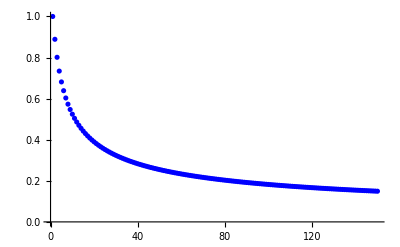

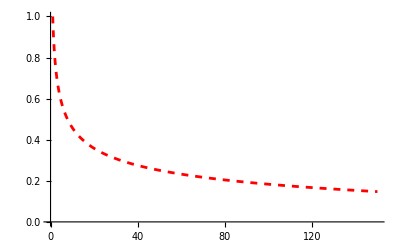

-Graphics-

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_fids_against_k.pdf

```mathematica
plt = ListPlot[{{1,0.9999999999999996},{2,0.8888888888888885},{3,0.8012263810222657},{4,0.734109105839151},{5,0.681372020154753},{6,0.6386613705526571},{7,0.6031602888592883},{8,0.5730328592001143},{9,0.5470396675485579},{10,0.5243101592180128},{11,0.5042115299779354},{12,0.4862708562702818},{13,0.4701265310003641},{14,0.45549664334150636},{15,0.44215769583475323},{16,0.42992988687451034},{17,0.4186666911359205},{18,0.40824732773061534},{19,0.39857121455855227},{20,0.38955381759459984},{21,0.38112349821606},{22,0.37321908660041503},{23,0.365787991355977},{24,0.35878471064353196},{25,0.3521696476845395},{26,0.3459081596948952},{27,0.33996978772208625},{28,0.33432762805120025},{29,0.3289578153999319},{30,0.3238390951283667},{31,0.318952466882763},{32,0.3142808859832216},{33,0.3098090118071578},{34,0.3055229946658185},{35,0.3014102943986995},{36,0.29745952525146535},{37,0.2936603226497024},{38,0.2900032283056733},{39,0.2864795907478173},{40,0.2830814788834697},{41,0.2798016066225007},{42,0.27663326692661677},{43,0.2735702739215558},{44,0.27060691193203146},{45,0.26773789048146157},{46,0.2649583044483971},{47,0.26226359869504573},{48,0.2596495365865771},{49,0.25711217190483254},{50,0.25464782373236644},{51,0.25225305394220754},{52,0.24992464697972788},{53,0.24765959166571663},{54,0.24545506478608645},{55,0.24330841626431585},{56,0.24121715573947416},{57,0.2391789403948097},{58,0.23719156390154436},{59,0.23525294635902871},{60,0.23336112512678903},{61,0.23151424645659763},{62,0.2297105578430735},{63,0.22794840102133682},{64,0.2262262055476462},{65,0.2245424829068006},{66,0.22289582109570072},{67,0.22128487963852345},{68,0.21970838499308157},{69,0.21816512631291635},{70,0.2166539515328694},{71,0.21517376374929678},{72,0.2137235178691225},{73,0.21230221750455813},{74,0.21090891209216167},{75,0.2095426942177471},{76,0.20820269712952416},{77,0.20688809242450057},{78,0.20559808789354153},{79,0.2043319255128392},{80,0.20308887956996027},{81,0.2018682549137808},{82,0.20066938531918557},{83,0.19949163195725395},{84,0.19833438196335407},{85,0.19719704709559066},{86,0.19607906247712645},{87,0.19497988541598976},{88,0.19389899429714433},{89,0.19283588754127598},{90,0.19179008262590125},{91,0.19076111516426553},{92,0.18974853803809844},{93,0.18875192058050863},{94,0.1877708478056467},{95,0.18680491968206253},{96,0.1858537504468099},{97,0.18491696795747323},{98,0.18399421307998967},{99,0.18308513910973412},{100,0.18218941122360063},{101,0.18130670596166842},{102,0.18043671073593595},{103,0.1795791233648626},{104,0.17873365163219102},{105,0.1779000128681369},{106,0.17707793355215257},{107,0.17626714893562623},{108,0.1754674026833218},{109,0.17467844653270845},{110,0.17390003996999912},{111,0.17313194992181039},{112,0.17237395046183235},{113,0.17162582253149197},{114,0.17088735367372054},{115,0.17015833777936595},{116,0.1694385748454099},{117,0.16872787074419324},{118,0.16802603700345065},{119,0.16733289059606743},{120,0.1666482537396117},{121,0.16597195370450457},{122,0.16530382263089075},{123,0.1646436973535091},{124,0.16399141923425764},{125,0.16334683400184355},{126,0.1627097915984806},{127,0.16208014603309207},{128,0.1614577552405701},{129,0.1608424809471697},{130,0.16023418854134605},{131,0.15963274694988328},{132,0.15903802851938342},{133,0.15844990890217173},{134,0.1578682669471937},{135,0.15729298459502075},{136,0.1567239467772142},{137,0.15616104131946118},{138,0.1556041588487854},{139,0.155053192704194},{140,0.15450803885071088},{141,0.1539685957970284},{142,0.15343476451581073},{143,0.15290644836764347},{144,0.15238355302720263},{145,0.151865986412597},{146,0.15135365861734082},{147,0.15084648184448862},{148,0.15034437034354795},{149,0.14984724034960012},{150,0.14935501002442889}},PlotStyle->{Blue},PlotRange->Full
, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]
(*pltfit = Plot[Exp[-0.05(k-1)],{k,0,20},
PlotStyle->{Blue,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
(*pltfit = Plot[ModelPoly[1,0.337382304689934,1,k],{k,0,100},
PlotStyle->{Blue,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
(*pltfit = Plot[ModelExpSimp[1,0.03715555947927945,k],{k,0,70},
PlotStyle->{Red,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
(*pltfit = LogPlot[ModelExp[0.41649069075555173,0.5756472374177177,0.19147556093490667,k],{k,0,20},
PlotStyle->{Blue,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
pltfit = Plot[ k^-a1 Exp[-a2 (k-1)] /. {a1->0.3324782014721347,a2->0.0016689433844058249,a3->0.},{k,1,150},PlotRange->{0,1},
PlotStyle->{Red,Opacity[1],Dashed}, BaseStyle->texStyle,FrameLabel ->  {MaTeX @"k","|F^{(k)}_\infty|"(*"F^{(k)}_\\infty (t)"*)},PlotLegends->Placed[LineLegend[Automatic,MaTeX @ {"S_\\phi"},LegendLayout-> "Column",Spacings->0],{0.5,0.5}]]
plts=Show[plt,pltfit,BaseStyle-> texStyle,Epilog-> Inset[Column[{PointLegend[{Blue},  MaTeX @{"~~~~ |F^{(k)}_\infty|" (*F_\\infty^{(k)}(t_\\infty^{(k)})*) (*\\langle 1 |e^{-i R_{k}\\frac{t}{\\sqrt{n}} } | k+1 \\rangle*) }],LineLegend[{Directive[{Dashed,Red}]}, MaTeX @{"k^{-0.3324} e^{-0.0017 (k-1)}"}]}],Scaled[{0.65,0.76}]], Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"k","\\mathrm{Fidelity}"},ImageSize->550]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_fids_against_k.pdf",plts]
```

```mathematica
FindFit[Table[tF150[[i]][[1]],{i,1,150,1} ], a0  t^-a1 Exp[-a2 (t-1)], {a0,a1,a2},t]
```

{a0→1.58308,a1→0.296748,a2→0.000900362}

```mathematica
FindFit[Table[tF150[[i]][[1]],{i,1,150,1} ], π/2  t^-a1 Exp[-a2 (t-1)], {a1,a2},t]
```

{a1→0.293565,a2→0.000969252}

```mathematica
FindFit[Table[tF150[[i]][[1]],{i,1,150,1} ], a0 t^-a1 , {a0,a1},t]
```

{a0→1.63224,a1→0.319604}

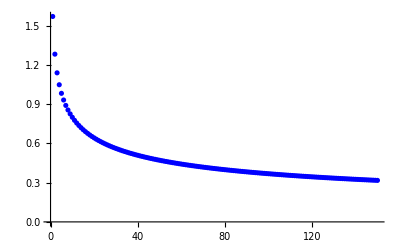

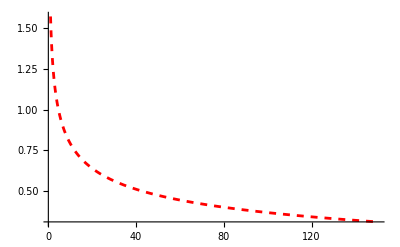

-Graphics-

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_times_against_k.pdf

```mathematica
plt = ListPlot[Table[tF150[[i]][[1]],{i,1,150,1} ],PlotStyle->{Blue},PlotRange->Full,BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]
(*pltfit = Plot[Exp[-0.05(k-1)],{k,0,20},
PlotStyle->{Blue,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
(*pltfit = Plot[ModelPoly[1,0.337382304689934,1,k],{k,0,100},
PlotStyle->{Blue,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
(*pltfit = Plot[ModelExpSimp[1,0.03715555947927945,k],{k,0,70},
PlotStyle->{Red,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
(*pltfit = LogPlot[ModelExp[0.41649069075555173,0.5756472374177177,0.19147556093490667,k],{k,0,20},
PlotStyle->{Blue,Opacity[0.6],Dashed}, BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","F^{(k)}_\\infty (t)"}]*)
pltfit = Plot[ a0 k^-a1 Exp[-a2 (k-1)] /. {a0->π/2,a1->0.293565,a2->0.000969252},{k,1,150},PlotRange->Full,
PlotStyle->{Red,Opacity[1],Dashed},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"k","t/\\sqrt{n}"}]
plts=Show[plt,pltfit,BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"k","\\mathrm{Time}"},ImageSize->550,BaseStyle->texStyle,Epilog-> Inset[Column[{PointLegend[{Blue},  MaTeX @{"~~~~t^{(k)}_\\infty / \\sqrt{n}"(*\\langle 1 |e^{-i R_{k}\\frac{t}{\\sqrt{n}} } | k+1 \\rangle*) }],LineLegend[{Directive[{Dashed,Red}]}, MaTeX @{"\\frac{\\pi}{2} k^{-0.2967} e^{-0.0009 (k-1)}"}]}],Scaled[{0.62,0.76}]]]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_times_against_k.pdf",plts]
```

```mathematica
FullSimplify[(k!)/((i-1)!(k-(i-1))!) (((n-k)!)/((n-k-(i-1))!(i-1)!))]
```

(k! (-k+n)!)/(Gamma[i]^2 Gamma[2-i+k] Gamma[2-i-k+n])

```mathematica
FullSimplify[Expand[Binomial[k,i-1]]Binomial[n-k,i-1]]
```

Binomial[k,-1+i] Binomial[-k+n,-1+i]

```mathematica
FindFit[tF150, a1 x + a2 x^2 + a3 x^3+a4 x^4 + a5 x^5+a6 x^6,{a1,a2,a3, a4, a5, a6},x]
```

{a1→0.269844,a2→0.856565,a3→-1.03991,a4→1.33182,a5→-0.961297,a6→0.238179}

```mathematica
FindFit[tF150, a1 x + a2 x^2 + a3 x^3+a4 x^4 ,{a1,a2,a3, a4},x]
```

{a1→0.296109,a2→0.592163,a3→-0.118644,a4→-0.0768694}

```mathematica
FindFit[tF150, a1 x + a2 x^2 + a3 x^3 ,{a1,a2,a3},x]
```

{a1→0.255815,a2→0.764376,a3→-0.330945}

```mathematica
tmax= 2.2;
plt = Plot[{FidelityAsymptotic[1,t],FidelityAsymptotic[2,t],FidelityAsymptotic[3,t],FidelityAsymptotic[4,t],FidelityAsymptotic[5,t],FidelityAsymptotic[6,t],FidelityAsymptotic[7,t],FidelityAsymptotic[8,t],FidelityAsymptotic[9,t],FidelityAsymptotic[10,t]},{t,0,tmax}
, PlotLegends->{MaTeX @ "k=1",MaTeX @ "k=2",MaTeX @"k=3",MaTeX @"k=4",MaTeX @"k=5",MaTeX @"k=6",MaTeX @"k=7",MaTeX @"k=8",MaTeX @"k=9",MaTeX @"k=10" },PlotStyle->{{Blue,Opacity[1]},{Blue,Opacity[0.9]},{Blue,Opacity[0.8]},{Blue,Opacity[0.7]},{Blue,Opacity[0.6]},{Blue,Opacity[0.5]},{Blue,Opacity[0.4]},{Blue,Opacity[0.3]},{Blue,Opacity[0.2]},{Blue,Opacity[0.1]}}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"}];
(*plt2 = ListPlot[Table[FindMaxtF[k],{k,1,10,1}],PlotStyle->{Red}];*)
plt2 = ListPlot[tF150,PlotStyle->{Red}];
(*plt3 = Plot[(1/1.568)x ,{x,0,2},PlotStyle->{Red, Dashed, Opacity[0.6]}];*)
plt3 = Plot[ a1 x + a2 x^2 + a3 x^3+a4 x^4+ a5 x^5+a6 x^6/. {a1->0.26984372009590063,a2->0.8565651886029284,a3->-1.039905824508839,a4->1.3318236440402893,a5->-0.9612969096049231,a6->0.23817853233229108} ,{x,0,1.567},PlotStyle->{Red, Dashed, Opacity[0.6]}];
pltks=Show[plt,plt2,plt3,BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"},Epilog-> Inset[Column[{PointLegend[{Blue},  MaTeX @{"~~~~t~\\textrm{for}~\\max_{t} \\left\\{ F_\\infty^{(k)}(t) \\right\\}"(*\\langle 1 |e^{-i R_{k}\\frac{t}{\\sqrt{n}} } | k+1 \\rangle*) }],LineLegend[{Directive[{Dashed,Red}]}, MaTeX @{"1.5831 k^{-0.2967} e^{-0.0009 (k-1)}"}]}],Scaled[{0.15,0.8}]],ImageSize->600]
```

```mathematica
tmax= 2.2;
plt = Plot[{FidelityAsymptotic[1,t],FidelityAsymptotic[2,t],FidelityAsymptotic[3,t],FidelityAsymptotic[4,t],FidelityAsymptotic[5,t],FidelityAsymptotic[6,t],FidelityAsymptotic[7,t],FidelityAsymptotic[8,t],FidelityAsymptotic[9,t],FidelityAsymptotic[10,t]},{t,0,tmax}
, PlotLegends->{MaTeX @ "k=1",MaTeX @ "k=2",MaTeX @"k=3",MaTeX @"k=4",MaTeX @"k=5",MaTeX @"k=6",MaTeX @"k=7",MaTeX @"k=8",MaTeX @"k=9",MaTeX @"k=10" },PlotStyle->{{Blue,Opacity[1]},{Blue,Opacity[0.9]},{Blue,Opacity[0.8]},{Blue,Opacity[0.7]},{Blue,Opacity[0.6]},{Blue,Opacity[0.5]},{Blue,Opacity[0.4]},{Blue,Opacity[0.3]},{Blue,Opacity[0.2]},{Blue,Opacity[0.1]}}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"}];
(*plt2 = ListPlot[Table[FindMaxtF[k],{k,1,10,1}],PlotStyle->{Red}];*)
plt2 = ListPlot[tF150,PlotStyle->{Red}];
(*plt3 = Plot[(1/1.568)x ,{x,0,2},PlotStyle->{Red, Dashed, Opacity[0.6]}];*)
plt3 = Plot[  a1 x + a2 x^2 + a3 x^3/. {a1->0.25581501228394254,a2->0.764375806874804,a3->-0.33094474728476964} ,{x,0,1.567},PlotStyle->{Red, Dashed, Opacity[0.6]}];
pltks=Show[plt,plt2,plt3,BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"},Epilog-> Inset[Column[{LineLegend[{Directive[{Dashed,Red}]}, MaTeX @{"0.256 x + 0.764 x^2 - 0.331 x^3"}],PointLegend[{Red},  MaTeX @{"~~\\max_{t} \\left\\{ F^{(k)}_{\\infty} (t) \\right\\} \\textrm{ for } k" }]}],Scaled[{0.27,0.83}]],ImageSize->700]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_fidelities_against_times_with_maximum_fidelities_indicated.pdf",pltks]
```

-Graphics-

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_fidelities_against_times_with_maximum_fidelities_indicated.pdf

```mathematica
tmax= 2.2;
plt = Plot[{FidelityAsymptotic[1,t],FidelityAsymptotic[2,t],FidelityAsymptotic[3,t],FidelityAsymptotic[4,t],FidelityAsymptotic[5,t],FidelityAsymptotic[6,t],FidelityAsymptotic[7,t],FidelityAsymptotic[8,t],FidelityAsymptotic[9,t],FidelityAsymptotic[10,t]},{t,0,tmax}
, PlotLegends->{MaTeX @ "k=1",MaTeX @ "k=2",MaTeX @"k=3",MaTeX @"k=4",MaTeX @"k=5",MaTeX @"k=6",MaTeX @"k=7",MaTeX @"k=8",MaTeX @"k=9",MaTeX @"k=10" },PlotStyle->{{Blue,Opacity[1]},{Blue,Opacity[0.9]},{Blue,Opacity[0.8]},{Blue,Opacity[0.7]},{Blue,Opacity[0.6]},{Blue,Opacity[0.5]},{Blue,Opacity[0.4]},{Blue,Opacity[0.3]},{Blue,Opacity[0.2]},{Blue,Opacity[0.1]}}, PlotRange->{0,1},BaseStyle->texStyle,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"},AspectRatio->0.7];
(*plt2 = ListPlot[Table[FindMaxtF[k],{k,1,10,1}],PlotStyle->{Red}];*)
plt2 = ListPlot[tF150,PlotStyle->{Red}];
(*plt3 = Plot[(1/1.568)x ,{x,0,2},PlotStyle->{Red, Dashed, Opacity[0.6]}];*)
plt3 = Plot[  a1 x + a2 x^2 + a3 x^3/. {a1->0.25581501228394254,a2->0.764375806874804,a3->-0.33094474728476964} ,{x,0,1.567},PlotStyle->{Red, Dashed, Opacity[0.6]}];
pltks=Show[plt,plt2,plt3,BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"\\frac{t}{\\sqrt{n}}","F^{(k)}_\\infty (t)"},Epilog-> Inset[Column[{LineLegend[{Directive[{Dashed,Red}]}, MaTeX @{"0.256 x + 0.764 x^2 - 0.331 x^3"}],PointLegend[{Red},  MaTeX @{"~|F^{(k)}_\\infty| \\textrm{ for } k" }]}],Scaled[{0.31,0.88}]],ImageSize->635]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_fidelities_against_times_with_maximum_fidelities_indicated_column.pdf",pltks]
```

-Graphics-

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_asymptotic_fidelities_against_times_with_maximum_fidelities_indicated_column.pdf

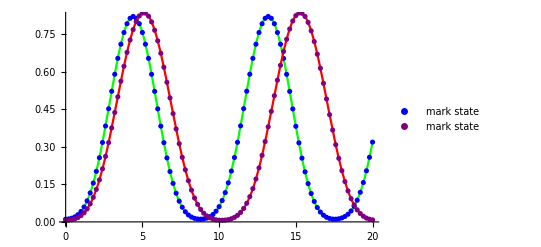

```mathematica
k= 2;
tmax= 20;
gamma[n_] := N[1/(n-2)];
pltn14 = ListPlot[Fidelities[14,k,gamma[14],tmax],PlotLegends->{"n=14"}, PlotStyle->Blue];
plta14 = Plot[FidelityAnalytical[14,k,gamma[14],t],{t,0,tmax},PlotLegends->{"mark state"}, PlotStyle->Green];
pltn18 = ListPlot[Fidelities[18,k,gamma[18],tmax],PlotLegends->{"mark state"},PlotStyle->Purple];
plta18 = Plot[FidelityAnalytical[18,k,gamma[18],t],{t,0,tmax}, PlotStyle->Red];
Show[plta14, pltn14, plta18, pltn18]
```

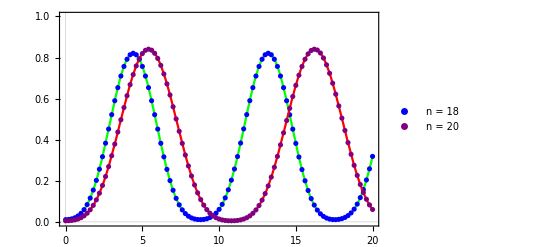

```mathematica
k= 2;
tmax= 20;
gamma[n_] := N[1/(n-2)];
pltn14 = ListPlot[Fidelities[14,k,gamma[14],tmax],PlotLegends->{"n = 14"}, PlotStyle->Blue,PlotTheme-> "Scientific", PlotRange->{0,1}];
plta14 = Plot[FidelityAnalytical[14,k,gamma[14],t],{t,0,tmax},PlotLegends->{""}, PlotStyle->Green,PlotTheme-> "Scientific", PlotRange->{0,1}];
pltn18 = ListPlot[Fidelities[20,k,gamma[20],tmax],PlotLegends->{"n = 20"},PlotStyle->Purple,PlotTheme-> "Scientific", PlotRange->{0,1}];
plta18 = Plot[FidelityAnalytical[20,k,gamma[20],t],{t,0,tmax}, PlotStyle->Red,PlotTheme-> "Scientific", PlotRange->{0,1}];
Show[plta14, pltn14, plta18, pltn18]
```

```mathematica
Clear[γ]
```

```mathematica
γ Hsearch[n,3]+ Hmarked[3] // MatrixForm
```

(3/2 | √3 √(-3+n) γ | 0 | 0
√3 √(-3+n) γ | 1/2+(-3+n) γ | 2 √2 √(-4+n) γ | 0
0 | 2 √2 √(-4+n) γ | -1/2+2 (-5+n) γ | 3 √(-5+n) γ
0 | 0 | 3 √(-5+n) γ | -3/2+3 (-6+n) γ)

```mathematica
FidelityAnalytical[nbits,k,γ,0.1]
```

Abs[{1,0,0}.MatrixExp[(0.+0.1 ⅈ) HsearchTotal[14,2,0.0833333]].{1/(√91),2 √(6/91),√(66/91)}]^2

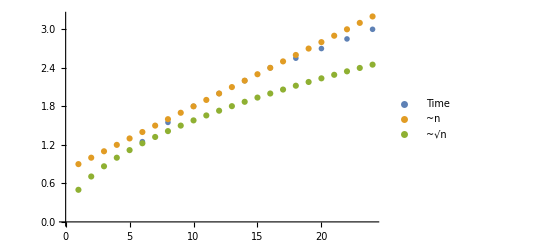

```mathematica
ListPlot[{{{6,1.25},{8,1.55},{10,1.8},{12,2},{14,2.2},{16,2.4},{18,2.55},{20,2.7},{22,2.85},{24,3}},Table[{n,n/10 +0.8},{n,1,24}],Table[{n,(√n)/2 },{n,1,24}]},PlotMarkers->{"OpenMarkers",None,None}, PlotLegends->{"Time","~n","~√n"}]
```

```mathematica
Hsearch[n_,k_] := Table[Table[If[i==j,(Max[i,j]-1)(n-k-Max[i,j]+1),If[Abs[j-i]==1,Min[i,j]Sqrt[(k-Min[i,j]+1)(n-k-Min[i,j]+1)],0]],{i,1,k+1}],{j,1,k+1}];
```

```mathematica
Hsearch[n,2]
```

{{0,√2 √(-2+n),0},{√2 √(-2+n),-3+n,2 √(-3+n)},{0,2 √(-3+n),2 (-4+n)}}

```mathematica
Hsearch[n,3] // MatrixForm
```

(0 | √3 √(-3+n) | 0 | 0
√3 √(-3+n) | -4+n | 2 √2 √(-4+n) | 0
0 | 2 √2 √(-4+n) | 2 (-5+n) | 3 √(-5+n)
0 | 0 | 3 √(-5+n) | 3 (-6+n))

Part::partd: Part specification {0.,1/153}⟦All,2⟧ is longer than depth of object.

{0.,1/153}⟦All,2⟧

Part::partd: Part specification {0.,1/153}⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification {0.,1/153}⟦All,2⟧ is longer than depth of object.

{0.,1/153}

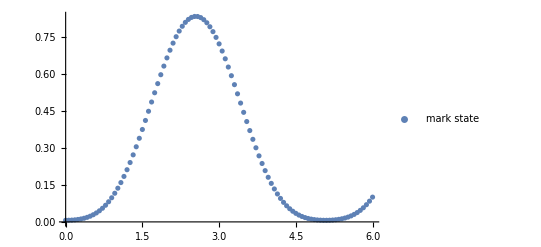

```mathematica
nodes = 18;
fids = Fidelities[nodes,2,N[4/(2(nodes-2))],6];
markfids = fids[[1]];
maxfidelity=Max[markfids[[All,2]]]
time = markfids[[All,1]][[Ordering[markfids[[All,2]],-1][[1]]]]
ListPlot[fids,PlotLegends->{"mark state","init state", "init - mark"}]
```

```mathematica
0.995 * 0.995
```

0.990025

```mathematica
Binomial[n,2]
```

1/2 (-1+n) n

```mathematica
With[{k=3, ϵ=0.01},Ceiling[s /. Sort[NSolve[Sum[(-1)^(i+1)Binomial[k,i]((k-i)/k)^s,{i,1,k}]==ϵ, s,PositiveReals]][[-1]]]]
```

15

```mathematica
With[{k=1,F=0.9, ϵ=0.01},Ceiling[s /. NSolve[Sum[(-1)^(i+1)Binomial[k,i]((k-i)/i)^s,{i,1,k}]==ϵ, s,PositiveReals]][[1]]]
```

s

```mathematica
With[{F=0.9, ϵ=0.01},Ceiling[x /. NSolve[(1-F)^x+x F (1-F)^(x-1)==ϵ, x,PositiveReals]][[1]]]
```

4

```mathematica
rtrials[F_,ϵ_]:= Ceiling[x /. NSolve[(1-F)^x+x F (1-F)^(x-1)==ϵ, x,PositiveReals]][[1]]
strials[k_,ϵ_]:= Ceiling[s /. Sort[NSolve[Sum[(-1)^(i+1)Binomial[k,i]((k-i)/k)^s,{i,1,k}]==ϵ, s,PositiveReals]][[-1]]]
```

```mathematica
t1subspace[n_,k_,ϵr_,ϵs_]:= strials[k,ϵs]rtrials[FindMaxγ0[n,1][[2]],ϵr] ((π √n)/2)
tksubspace[n_,k_,ϵ_]:= rtrials[FindMaxγ0[n,1][[2]],ϵ] (π/2)k^-0.2967 ⅇ^(-0.00009(k-1))√n
```

```mathematica
t1subspace[n_,k_,ϵr_,ϵs_]:= strials[k,ϵs] ((π √n)/2)
tksubspace[n0_,k0_,ϵ0_]:= Module[{n=n0,k=k0,ϵ=ϵ0},
F=FindMaxγ0[n,1][[2]];
 rtrials[k^-0.3324 ⅇ^(-0.0017(k-1)),ϵ] ]
```

```mathematica
Clear[k]
```

```mathematica
plottimes[nmax_,subspace_,ϵr_,ϵs_]:=ListPlot[Table[{n,t1subspace[n,subspace,ϵr,ϵs]},{n,subspace+6,nmax}]]
```

```mathematica
N[t1subspace[10,2,0.005,0.005]]
```

89.4113

```mathematica
tksubspace[10,2,0.99]
```

8.08714

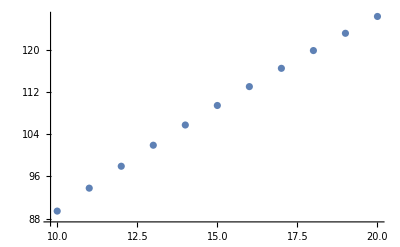

```mathematica
ListPlot[Table[{n,t1subspace[n,2,0.005,0.005]},{n,10,20}]]
```

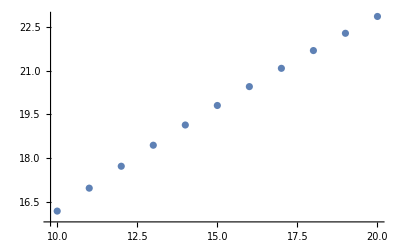

```mathematica
ListPlot[Table[{n,tksubspace[n,2,0.01]},{n,10,20}]]
```

```mathematica
strials[2,0.005]
```

9

```mathematica
Table[{n,t1subspace[n,2,0.005,0.005]},{n,10,50}]
```

$Aborted

```mathematica
FindMaxγ0[20,1][[2]]
```

0.999973

```mathematica
FindMaxγ0t[nbits0_,k0_]:= Module[{nbits=nbits0,k=k0}, 
max[γ_]:=Max[Transpose[Fidelities[nbits,k, γ,10]][[2]]];
maxγ = GoldenSearch[max, 0.5 /nbits,1.5 /nbits,0.001,15];
Fids =Transpose[Fidelities[nbits,k, maxγ[[1]],10]][[2]];
t = N[Position[Fids,Max[Fids]][[1]][[1]] * 10/100];
{maxγ[[1]],maxγ[[2]],t}
]
```

```mathematica
t1subspace[n_,k_,ϵr_,ϵs_]:= strials[k,ϵs] ((π √n)/2)
tksubspace[n0_,k0_,ϵ0_]:= Module[{n=n0,k=k0,ϵ=ϵ0},
Ft=FindMaxγ0t[n,k];
 rtrials[Ft[[2]],ϵ]Ft[[3]]
]
```

```mathematica
t1subspacenFk2 =N[Table[{n,t1subspace[n,2,0.005,0.005]},{n,6,20}]]
tksubspacenFk2 =Table[{n,tksubspace[n,2,0.01]},{n,6,20}]
```

{{6.,69.2577},{7.,74.8069},{8.,79.9719},{9.,84.823},{10.,89.4113},{11.,93.7754},{12.,97.9452},{13.,101.945},{14.,105.793},{15.,109.506},{16.,113.097},{17.,116.578},{18.,119.958},{19.,123.245},{20.,126.447}}

{{6,15.6607},{7,16.9155},{8,18.0834},{9,19.1803},{10,20.2179},{11,21.2047},{12,22.1476},{13,23.0519},{14,23.9221},{15,24.7617},{16,25.5738},{17,26.3609},{18,27.1251},{19,27.8684},{20,28.5924}}

```mathematica
t1subspacenFk3 =Table[{n,t1subspace[n,3,0.005,0.005]},{n,6,20}]
tksubspacenFk3 =Table[{n,tksubspace[n,3,0.01]},{n,6,20}]
```

{{6,16 √6 π},{7,16 √7 π},{8,32 √2 π},{9,48 π},{10,16 √10 π},{11,16 √11 π},{12,32 √3 π},{13,16 √13 π},{14,16 √14 π},{15,16 √15 π},{16,64 π},{17,16 √17 π},{18,48 √2 π},{19,16 √19 π},{20,32 √5 π}}

{{6,19.4381},{7,20.9955},{8,22.4452},{9,23.8067},{10,25.0945},{11,26.3193},{12,27.4896},{13,28.6121},{14,29.6922},{15,30.7343},{16,31.7423},{17,32.7192},{18,33.6678},{19,34.5903},{20,35.4889}}

```mathematica
t1subspacenFk4 =Table[{n,t1subspace[n,4,0.005,0.005]},{n,8,20}]
tksubspacenFk4 =Table[{n,tksubspace[n,4,0.01]},{n,8,20}]
```

{{8,48 √2 π},{9,72 π},{10,24 √10 π},{11,24 √11 π},{12,48 √3 π},{13,24 √13 π},{14,24 √14 π},{15,24 √15 π},{16,96 π},{17,24 √17 π},{18,72 √2 π},{19,24 √19 π},{20,48 √5 π}}

{{8,23.5508},{9,24.9794},{10,26.3306},{11,27.6158},{12,28.8438},{13,30.0215},{14,31.1548},{15,32.2483},{16,33.3059},{17,34.331},{18,35.3263},{19,36.2943},{20,37.2371}}

```mathematica
t1subspacenFk4 = {{8,48 √2 π},{9,72 π},{10,24 √10 π},{11,24 √11 π},{12,48 √3 π},{13,24 √13 π},{14,24 √14 π},{15,24 √15 π},{16,96 π}}
tksubspacenFk4 = {{8,11.775419908726573},{9,12.489718903169454},{10,16.456649612198117},{11,17.25987972450928},{12,18.027356427119102},{13,18.763467467295552},{14,19.471770413655882},{15,20.155197212828025},{16,20.81619817194909}}
```

{{8,48 √2 π},{9,72 π},{10,24 √10 π},{11,24 √11 π},{12,48 √3 π},{13,24 √13 π},{14,24 √14 π},{15,24 √15 π},{16,96 π}}

{{8,11.7754},{9,12.4897},{10,16.4566},{11,17.2599},{12,18.0274},{13,18.7635},{14,19.4718},{15,20.1552},{16,20.8162}}

```mathematica
t1subspacenFk5 =Table[{n,t1subspace[n,5,0.005,0.005]},{n,10,20}]
tksubspacenFk5 =Table[{n,tksubspace[n,5,0.01]},{n,10,20}]
```

$Aborted

{{10,27.7218},{11,29.0749},{12,30.3677},{13,31.6077},{14,32.8009},{15,33.9521},{16,35.0656},{17,36.1448},{18,37.1927},{19,38.2119},{20,39.2046}}

```mathematica
t1subspacenFk5 ={{10,31 √10 π},{11,31 √11 π},{12,62 √3 π},{13,31 √13 π},{14,31 √14 π}} 
tksubspacenFk5={{10,15.401007596160898},{11,16.15271303758927},{12,16.870958537451475},{13,17.559850382907804},{14,18.222717935802223}}
```

{{10,31 √10 π},{11,31 √11 π},{12,62 √3 π},{13,31 √13 π},{14,31 √14 π}}

{{10,15.401},{11,16.1527},{12,16.871},{13,17.5599},{14,18.2227}}

```mathematica
t1subspacenFk2 =N[Table[{n,t1subspace[n,2,0.005,0.01]},{n,4,20}]]
tksubspacenFk2 =Table[{n,tksubspace[n,2,0.01]},{n,4,20}]
t1subspacenFk3 =N[Table[{n,t1subspace[n,3,0.005,0.01]},{n,6,18}]]
tksubspacenFk3 =Table[{n,tksubspace[n,3,0.01]},{n,6,18}]
t1subspacenFk4 =N[Table[{n,t1subspace[n,4,0.005,0.01]},{n,8,16}]]
tksubspacenFk4 =Table[{n,tksubspace[n,4,0.01]},{n,8,16}]
t1subspacenFk5 =N[Table[{n,t1subspace[n,5,0.005,0.01]},{n,10,14}]]
tksubspacenFk5 =Table[{n,tksubspace[n,5,0.01]},{n,10,14}]
```

{{4.,25.1327},{5.,28.0993},{6.,30.7812},{7.,33.2475},{8.,35.5431},{9.,37.6991},{10.,39.7384},{11.,41.6779},{12.,43.5312},{13.,45.3087},{14.,47.0191},{15.,48.6693},{16.,50.2655},{17.,51.8125},{18.,53.3146},{19.,54.7755},{20.,56.1985}}

{{4,9.3},{5,9.9},{6,14.4},{7,15.2},{8,16.},{9,16.8},{10,17.6},{11,18.4},{12,18.8},{13,19.6},{14,20.4},{15,20.8},{16,21.6},{17,22.},{18,22.8},{19,23.2},{20,24.}}

{{6.,57.7147},{7.,62.339},{8.,66.6432},{9.,70.6858},{10.,74.5094},{11.,78.1461},{12.,81.621},{13.,84.9538},{14.,88.1607},{15.,91.255},{16.,94.2478},{17.,97.1484},{18.,99.9649}}

{{6,14.},{7,14.4},{8,15.2},{9,16.},{10,16.4},{11,17.2},{12,22.},{13,23.},{14,23.5},{15,24.},{16,25.},{17,25.5},{18,26.}}

{{8.,93.3005},{9.,98.9602},{10.,104.313},{11.,109.405},{12.,114.269},{13.,118.935},{14.,123.425},{15.,127.757},{16.,131.947}}

{{8,15.2},{9,15.6},{10,20.},{11,20.5},{12,21.5},{13,22.},{14,22.5},{15,23.},{16,23.5}}

{{10.,139.084},{11.,145.873},{12.,152.359},{13.,158.58},{14.,164.567}}

{{10,20.},{11,20.5},{12,21.},{13,21.5},{14,22.}}

```mathematica
t1subspaceNFk2 =Map[ {Binomial[#1[[1]],2],#1[[2]]}&,t1subspacenFk2 ];
tksubspaceNFk2 =Map[ {Binomial[#1[[1]],2],#1[[2]]}&,tksubspacenFk2 ];
t1subspaceNFk3 =Map[ {Binomial[#1[[1]],3],#1[[2]]}&,t1subspacenFk3 ];
tksubspaceNFk3 =Map[ {Binomial[#1[[1]],3],#1[[2]]}&,tksubspacenFk3 ];
t1subspaceNFk4 =Map[ {Binomial[#1[[1]],4],#1[[2]]}&,t1subspacenFk4 ];
tksubspaceNFk4 =Map[ {Binomial[#1[[1]],4],#1[[2]]}&,tksubspacenFk4 ];
t1subspaceNFk5 =Map[ {Binomial[#1[[1]],5],#1[[2]]}&,t1subspacenFk5 ];
tksubspaceNFk5 =Map[ {Binomial[#1[[1]],5],#1[[2]]}&,tksubspacenFk5 ];
```

```mathematica
pmsize=12;
tloc = {{1,0},{0,Sqrt[3]},{-1,0}};
```

```mathematica
ListPlot[{t1subspacenFk2,tksubspacenFk2,t1subspacenFk3,tksubspacenFk3,t1subspacenFk4,tksubspacenFk4,t1subspacenFk5,tksubspacenFk5},PlotLegends->Placed[{MaTeX @ "k=2\\textrm{, 1-subspace}",MaTeX @ "k=2\\textrm{, 2-subspace}", MaTeX @ "k=3\\textrm{, 1-subspace}",MaTeX @ "k=3\\textrm{, 3-subspace}",MaTeX @ "k=4\\textrm{, 1-subspace}",MaTeX @ "k=4\\textrm{, 4-subspace}",MaTeX @ "k=5\\textrm{, 1-subspace}",MaTeX @ "k=5\\textrm{, 5-subspace}"},{1.05,0.38}], Joined->True,PlotMarkers->{Graphics[{Blue,Disk[{0,0}]},ImageSize->pmsize],Graphics[{Blue,Triangle[tloc]},ImageSize->pmsize],Graphics[{DarkGreen,Disk[{0,0}]},ImageSize->pmsize],Graphics[{DarkGreen,Triangle[tloc]},ImageSize->pmsize],Graphics[{Orange,Disk[{0,0}]},ImageSize->pmsize],Graphics[{Orange,Triangle[tloc]},ImageSize->pmsize],Graphics[{Purple,Disk[{0,0}]},ImageSize->pmsize],Graphics[{Purple,Triangle[tloc]},ImageSize->pmsize]},PlotStyle-> {Blue,Blue,DarkGreen,DarkGreen,Orange,Orange,Purple,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"n","\\mathrm{Time~to~reach}~P_\\mathrm{success} > 0.99"},AspectRatio->1, ImageSize->720]
```

-Graphics-

```mathematica
Placed[{MaTeX @ "\\textrm{Repeated, }k=2",MaTeX @ "k\\textrm{-excitation, }k=2",MaTeX @  "\\textrm{Repeated, }k=3",MaTeX @ "k\\textrm{-excitation, }k=3",MaTeX @ "\\textrm{Repeated, }k=4",MaTeX @"k\\textrm{-excitation, }k=4",MaTeX @ "\\textrm{Repeated, }k=5", MaTeX @"k\\textrm{-excitation, }k=5"},{1.02,0.56}]
```

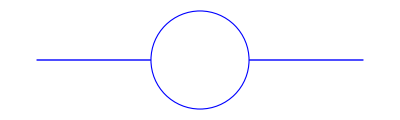
Placed[{-Graphics- | -Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1.02,0.56}]

```mathematica
Placed[{Grid[{{Show[Graphics[{Blue,Thick,Line[{{-0.5,0},{0.5,0}}]}],Graphics[{White,EdgeForm[Directive[Thick,Blue]],Disk[{0,0},0.15]},ImageSize->4]],MaTeX @ "\\textrm{Repeated, }k=2"}}],MaTeX @ "k\\textrm{-excitation, }k=2",MaTeX @  "\\textrm{Repeated, }k=3",MaTeX @ "k\\textrm{-excitation, }k=3",MaTeX @ "\\textrm{Repeated, }k=4",MaTeX @"k\\textrm{-excitation, }k=4",MaTeX @ "\\textrm{Repeated, }k=5", MaTeX @"k\\textrm{-excitation, }k=5"},{1.02,0.56}]
```

```mathematica
legendr[color_]:=Show[Graphics[{color,Thick,Line[{{-0.5,0},{0.5,0}}]}],Graphics[{White,EdgeForm[Directive[Thick,color]],Disk[{0,0},0.15]}]]
legendk[color_]:=Show[Graphics[{color,Thick,Line[{{-0.5,0},{0.5,0}}]}],Graphics[{color,EdgeForm[Directive[Thick,color]],Disk[{0,0},0.15]}]]
```

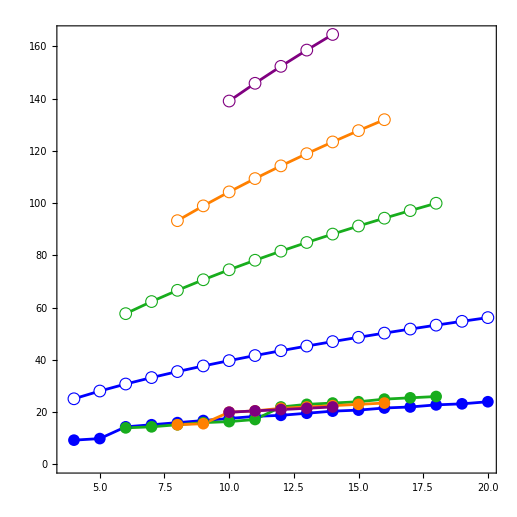

-Graphics-

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_time_P_success_n.pdf

/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_time_P_success_Nk.pdf

```mathematica
plttimen =ListPlot[{t1subspacenFk2,tksubspacenFk2,t1subspacenFk3,tksubspacenFk3,t1subspacenFk4,tksubspacenFk4,t1subspacenFk5,tksubspacenFk5}, Joined->True,PlotMarkers->{Graphics[{White,EdgeForm[Directive[Thick,Blue]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{Blue,Disk[{0,0}]},ImageSize->pmsize],Graphics[{White,EdgeForm[Directive[Thick,DarkGreen]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{DarkGreen,Disk[{0,0}]},ImageSize->pmsize],Graphics[{White,EdgeForm[Directive[Thick,Orange]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{Orange,Disk[{0,0}]},ImageSize->pmsize],Graphics[{White,EdgeForm[Directive[Thick,Purple]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{Purple,Disk[{0,0}]},ImageSize->pmsize]},PlotStyle-> {Blue,Blue,DarkGreen,DarkGreen,Orange,Orange,Purple,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"n","\\mathrm{Time~to~reach}~P_\\mathrm{success} > 0.99"},AspectRatio->1, ImageSize->517]
plttimeNk =ListPlot[{t1subspaceNFk2,tksubspaceNFk2,t1subspaceNFk3,tksubspaceNFk3,t1subspaceNFk4,tksubspaceNFk4,t1subspaceNFk5,tksubspaceNFk5},PlotLegends-> Placed[Grid[{
{legendr[Blue],MaTeX @ "\\textrm{Repeated, }k=2"},
{legendk[Blue],MaTeX @ "k\\textrm{-excitation, }k=2"},
{legendr[DarkGreen],MaTeX @ "\\textrm{Repeated, }k=3"},{legendk[DarkGreen],MaTeX @ "k\\textrm{-excitation, }k=3"},{legendr[Orange], MaTeX @ "\\textrm{Repeated, }k=4"}, 
{legendk[Orange], MaTeX @ "k\\textrm{-excitation, }k=4"},
{legendr[Purple],MaTeX @ "\\textrm{Repeated, }k=5" },
{legendk[Purple],MaTeX @ "k\\textrm{-excitation, }k=5" }
},ItemSize->{{1.2,8}}, Alignment->Left],{{1.02,0.56}}], Joined->True,PlotMarkers->{Graphics[{White,EdgeForm[Directive[Thick,Blue]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{Blue,Disk[{0,0}]},ImageSize->pmsize],Graphics[{White,EdgeForm[Directive[Thick,DarkGreen]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{DarkGreen,Disk[{0,0}]},ImageSize->pmsize],Graphics[{White,EdgeForm[Directive[Thick,Orange]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{Orange,Disk[{0,0}]},ImageSize->pmsize],Graphics[{White,EdgeForm[Directive[Thick,Purple]],Disk[{0,0}]},ImageSize->pmsize],Graphics[{Purple,Disk[{0,0}]},ImageSize->pmsize]},PlotStyle-> {Blue,Blue,DarkGreen,DarkGreen,Orange,Orange,Purple,Purple},BaseStyle-> texStyle, Frame->True,FrameStyle->Black,FrameLabel -> MaTeX @ {"N_k"},PlotRange->All,AspectRatio->1, ImageSize->774]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_time_P_success_n.pdf",plttimen]
Export["/Users/dylan/Documents/Physics/spatial_search_higher_subspace/plots/mathematica/plot_of_time_P_success_Nk.pdf",plttimeNk]
```

```mathematica
N[(0.72)2 Log[2]]
```

0.998132

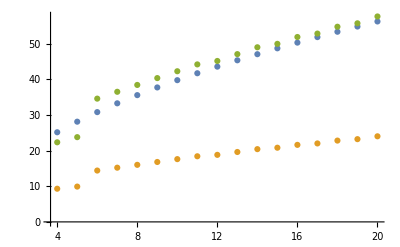

```mathematica
ListPlot[{t1subspacenFk2,tksubspacenFk2,Map[ {#1[[1]],(1.2)2#1[[2]]}&,tksubspacenFk2 ]}]
```

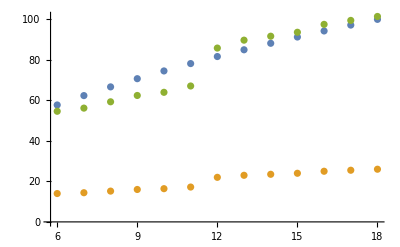

```mathematica
ListPlot[{t1subspacenFk3,tksubspacenFk3,Map[ {#1[[1]],(1.3)3 #1[[2]]}&,tksubspacenFk3 ]}]
```

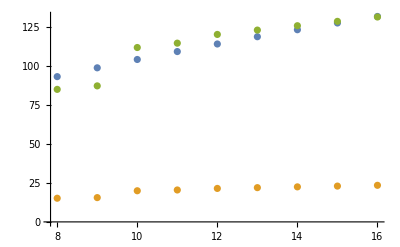

```mathematica
ListPlot[{t1subspacenFk4,tksubspacenFk4,Map[ {#1[[1]],(1.4)4 #1[[2]]}&,tksubspacenFk4 ]}]
```

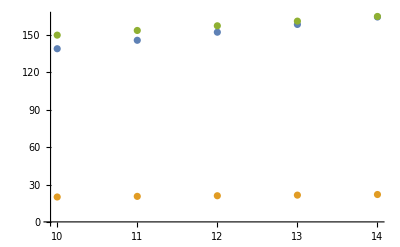

```mathematica
ListPlot[{t1subspacenFk5,tksubspacenFk5,Map[ {#1[[1]],(1.5)5 #1[[2]]}&,tksubspacenFk5 ]}]
```

```mathematica
Fit[{{2,1.2},{3,1.3},{4,1.4},{5,1.5}}, {Log[x]},x]
```

1.06701 Log[x]

```mathematica
Fit[{{2,1.2},{3,1.3},{4,1.4},{5,1.5}}, {1,Log[x]},x]
```

0.962941+0.323392 Log[x]

```mathematica
Fit[{{2,.2},{3,.3},{4,.4},{5,.5}}, {Log[x]},x]
```

0.294774 Log[x]

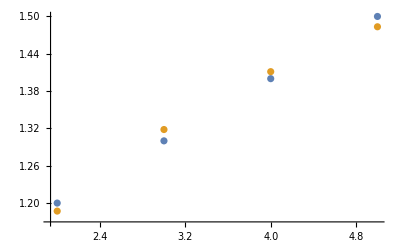

```mathematica
ListPlot[{{{2,1.2},{3,1.3},{4,1.4},{5,1.5}}, Table[{x,0.9629409210527118+0.3233919553226137 Log[x]},{x,2,5}]}]
```

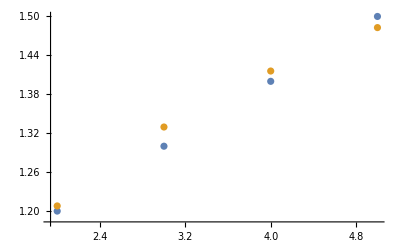

```mathematica
ListPlot[{{{2,1.2},{3,1.3},{4,1.4},{5,1.5}}, Table[{x,1+0.3 Log[x]},{x,2,5}]}]
```